# CFD Convergence Testing

Looking at CFD operator convergence factor over time.

```mathematica
Clear["`*"];
```

## Essential Modules and Initializations

### Defining Coefficients

```mathematica
Clear[coeffP12,coeffP6,coeffP8,coeffT4,coeffT6,coeffP10,coeffT8,coeffT42D,d2];

coeffVariables={
α,β,
α12,β12,
α21,α22,β22,
β31,α31,α32,β32,
β41,α41,α42,β42,
a,b,c,d,
a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1,
a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2,
a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3,
a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4
};
coeffAllZero={
α->0,β->0,
α12->0,β12->0,
α21->0,α22->0,β22->0,
β31->0,α31->0,α32->0,β32->0,
β41->0,α41->0,α42->0,β42->0,
a->0,b->0,c->0,d->0,
a1->0,b1->0,c1->0,d1->0,e1->0,f1->0,g1->0,h1->0,i1->0,j1->0,k1->0,
a2->0,b2->0,c2->0,d2->0,e2->0,f2->0,g2->0,h2->0,i2->0,j2->0,k2->0,
a3->0,b3->0,c3->0,d3->0,e3->0,f3->0,g3->0,h3->0,i3->0,j3->0,k3->0,
a4->0,b4->0,c4->0,d4->0,e4->0,f4->0,g4->0,h4->0,i4->0,j4->0,k4->0
};

centeredExplicitScheme=Join[{
a->1
},coeffAllZero
];

coeffKim24=Join[{α->0.5862704032801503,β->0.0954953355017055,a->0.6431406736919156,b->0.2586011023495066,c->0.007140953479797375,α12->43.65980335321481,β12->92.40143116322876,α21->0.08351537442980239,α22->1.961483362670730,β22->0.8789761422182460,β31->0.008073091519768687,α31->0.2162434143850924,α32->1.052242062502679,β32->0.2116022463346598,a1->-6.658527037451025,b1->-86.92242000231872,c1->47.58661913475775,d1->57.30693626084370,e1->-13.71254216556246,f1->2.659826729790792,g1->-0.2598929200600359,a2->-0.3199960780333493,b2->-1.438068456255548,c2->0.07735499170041915,d2->1.496612372811008,e2->0.2046919801608821,f2->-0.02229717539815850,g2->0.001702365014746567,a3->-0.03644974757120792,b3->-0.4997030280694729,c3->-0.7861024376433451,d3->0.7439822445654316,e3->0.5629384925762924,f3->0.01563884275691290,g3->-0.0003043666146108995},coeffAllZero];

coeffNateTestOperator=Join[{α->0.577046020129,β->0.0890083684509,a->0.65170784409,b->0.24815882627,c->0.00600963064985,α12->7.54033708428,β12->6.68314895992,α21->0.10810728338,α22->0.987941528443,β22->-0.0190910498621,β31->0.0108325025097,α31->0.238186806866,α32->1.12827907699,β32->0.288649699199,a1->-3.45139624553,b1->-6.50490079826,c1->7.66779401418,d1->2.52842591838,e1->-0.300598774934,f1->0.0717510137605,g1->-0.0110751276032,a2->-0.396496422553,b2->-1.04205354771,c2->1.14707986705,d2->0.349408266713,e2->-0.0673799703106,f2->0.0105041842665,g2->-0.00106237744537,a3->-0.0467868655168,b3->-0.51044828216,c3->-0.770033072248,d3->0.622893361976,e3->0.672712515935,f3->0.0330416895274,g3->-0.00137934751443},coeffAllZero];

coeffP4NateEvenBetter=Join[
{α->0.577046020129,β->0.0890083684509,a->0.65170784409*2,b->0.24815882627*4,c->0.00600963064985*6},coeffAllZero
];

coeffP4NateBoundary3=Join[
{α->0.577046020129,β->0.0890083684509,a->0.65170784409,b->0.24815882627,c->0.00600963064985,
α12->7.54033708428,β12->7.54033708428,α21->0.214028075093,α22->-2.66994888076,β22->-4.18758936272,β31->0.0108325025097,α31->0.238186806866,α32->1.12827907699,β32->0.288649699199,a1->-3.45139624553,b1->-6.50490079826,c1->7.66779401418,d1->2.52842591838,e1->-0.300598774933,f1->0.0717510137611,g1->-0.0110751276032,a2->-0.697452542301,b2->0.384399552143,c2->5.68251447958,d2->-3.85098987108,e2->-1.78768457384,f2->0.304508504933,g2->-0.0352955491234,a3->-0.0467868655168,b3->-0.510448282161,c3->-0.770033072248,d3->0.622893361976,e3->0.672712515935,f3->0.0330416895274,g3->-0.00137934751443},coeffAllZero
];

coeffP4Nate1=Join[{
α->0.567498,β->0.0827093,a->0.660388*2,b->0.237376*4,c->0.0050227*6
},coeffAllZero];

coeffP4Kim1=Join[{
α->0.5856396845642288,
β->0.09505833117193530,
a->0.6437151795729501*2,
b->0.2578941677285964*4,
c->0.007064833568673624*6
},coeffAllZero];

coeffP4Nate2=Join[{
α->0.462125,
β->0.0143368,
a->0.754521*2,
b->0.119357*4,
c->-0.0059121*6
},coeffAllZero];

coeffP4Kim2=Join[{
α->0.5864696980962217,
β->0.09564623994911990,
a->0.6429512471438849*2,
b->0.2588269491578893*4,
c->0.007170264195226098*6
},coeffAllZero];

(* This is for Nate's Scheme with free parameters *)
NateFreePars={β->-1/114,a06->0.19411653027075437,a17->-0.020069295598354353,a27->0.18761077427243267,a07->0.7973578396056882,a11->0.1387943278662136,a22->-0.029543768177269225};
coeffNateP6=Join[{a->-2/9 (-7+12 β),b->1/9 (1+114 β),α->1/3 (1+12 β),a1->1/60 (-227+600 a06+5400 a07),b1->1/6 (-65+1644 a06+14175 a07),c1->1/3 (35-375 a06-3528 a07),d1->-5/3 (-2+120 a06+945 a07),e1->5/12 (-1+120 a06+840 a07),f1->1/30 (1-300 a06-1575 a07),a2->(-36499-11820 a11+611400 a17)/64800,c2->1/288 (1331+780 a11+161112 a17),d2->1/81 (-263-240 a11-25725 a17),e2->1/32 (-29-20 a11-9800 a17),f2->1/225 (23+15 a11+14700 a17),g2->(-19-12 a11-29400 a17)/2592,a3->(-1663-1452 a22-1000512 a27)/16200,b3->(-1993-804 a22-89964 a27)/2700,d3->1/81 (67+12 a22-67473 a27),e3->1/216 (5-156 a22+169344 a27),f3->1/100 (-1-4 a22+15876 a27),g3->(1+3 a22-31752 a27)/2025,α12->-10 (-1+12 a06+105 a07),β12->-10 (-1+30 a06+252 a07),α21->(167+60 a11-4200 a17)/1080,α22->1/24 (-47-60 a11-5880 a17),β22->1/27 (-77-60 a11-14700 a17),β31->1/540 (13+12 a22+9072 a27),α31->1/45 (19+12 a22+5292 a27),α32->-2/27 (-5+12 a22-7938 a27),β32->1/36 (-1-12 a22+21168 a27)}/.NateFreePars,coeffAllZero];


coeffNJP8=Join[{a->40/27,b->25/54,α->4/9,β->1/36,a1->-79/20,b1->-77/5,c1->55/4,d1->20/3,e1->-5/4,f1->1/5,g1->-1/60,a2->-257/1080,b2->-107/60,c2->-5/24,d2->55/27,e2->5/24,f2->-1/60,g2->1/1080,a3->-34/675,b3->-127/225,c3->-7/12,d3->20/27,e3->4/9,f3->1/75,g3->-1/2700,a4->-1/600,b4->-101/600,c4->-17/24,d4->0,e4->17/24,f4->101/600,g4->1/600,α12->12,β12->15,α21->1/18,α22->5/2,β22->10/9,β31->1/90,α31->4/15,α32->8/9,β32->1/6,β41->1/20,α41->1/2,α42->1/2,β42->1/20},coeffAllZero];

coeffT4=Join[{α->1/4,α12->3,a->3/2,a1->-17/6,b1->3/2,c1->3/2,d1->-1/6},coeffAllZero];

coeffT42D=Join[{α->1/10,α12->10,a->6/5,a1->145/12,b1->-76/3,c1->29/2,d1->-4/3,e1->1/12},coeffAllZero];

coeffNJP62D=Join[{a->120/97,α->12/97,β->-1/194,a1->177/16,b1->-507/8,c1->783/8,d1->-201/4,e1->81/16,f1->-3/8,α12->11/2,β12->-131/4},coeffAllZero];

coeffT6=Join[{
α->1/3,
α12->5,
α21->1/8,α22->3/4,
a->14/9,b->1/9,c->0,d->0,
a1->-197/60,b1->-5/12,c1->5,d1->-5/3,e1->5/12,f1->-1/20,
a2->-43/96,b2->-5/6,c2->9/8,d2->1/6,e2->-1/96
},coeffAllZero];

coeffT8=Join[{
α->3/8,
α12->7,
α21->1/12,α22->5/4,
α31->13/55,α32->6/11,
a->25/16,b->1/5,c->-1/80,
a1->-503/140,b1->-63/20,c1->21/2,d1->-35/6,e1->35/12,f1->-21/20,g1->7/30,h1->-1/42,
a2->-79/240,b2->-77/60,c2->55/48,d2->5/9,e2->-5/48,f2->1/60,g2->-1/720,
a3->-1/66,b3->-2051/3300,c3->-53/132,d3->31/33,e3->7/66,f3->-1/132,g3->1/3300
},coeffAllZero];


coeffP6=Join[{
α->17/57,β->-1/114,
α12->8,β12->6,
a->30/19,b->0,c->0,d->0,
a1->-43/12,b1->-20/3,c1->9,d1->4/3,e1->-1/12
},coeffAllZero];

coeffP8=Join[{
α->4/9,β->1/36,
α12->12,β12->15,
α21->1/15,α22->2,β22->2/3,
a->40/27,b->25/54,
a1->-79/20,b1->-77/5,c1->55/4,d1->20/3,e1->-5/4,f1->1/5,g1->-1/60,
a2->-247/900,b2->-19/12,c2->1/3,d2->13/9,e2->1/12,f2->-1/300
},coeffAllZero];

coeffP10={
α->1/2,β->1/20,
α12->16,β12->28,
α21->1/21,α22->3,β22->5/3,
β31->1/90,α31->4/15,α32->8/9,β32->1,
β41->0,α41->0,α42->0,β42->0,
a->17/12,b->101/150,c->1/100,d->0,
a1->-1181/280,b1->-892/35,c1->77/5,d1->56/3,e1->-35/6,f1->28/15,g1->-7/15,h1->8/105,i1->-1/168,j1->0,k1->0,
a2->-544/2581,b2->-39/20,c2->-17/20,d2->95/36,e2->5/12,f2->-1/20,g2->1/180,h2->-1/2940,i2->0,j2->0,k2->0,
a3->-34/675,b3->-127/225,c3->-7/12,d3->20/27,e3->4/9,f3->1/75,g3->-1/2700,h3->0,i3->0,j3->0,k3->0,
a4->0,b4->0,c4->0,d4->0,e4->0,f4->0,g4->0,h4->0,i4->0,j4->0,k4->0
};

coeffP12={
α->8/15,β->1/15,
α12->20,β12->45,
α21->1/27,α22->4,β22->28/9,
β31->1/168,α31->4/21,α32->4/3,β32->5/12,
β41->1/42,α41->1/3,α42->5/6,β42->1/6,
a->308/225,b->182/225,c->4/175,d->-1/1575,
a1->-1590/359,b1->-4609/126,c1->711/56,d1->40,e1->-35/2,f1->42/5,g1->-7/2,h1->8/7,i1->-15/56,j1->5/126,k1->-1/360,
a2->-857/4963,b2->-621/280,c2->-83/35,d2->511/135,e2->7/6,f2->-7/30,g2->7/135,h2->-1/105,i2->1/840,j2->-1/13608,k2->0,
a3->-115/4024,b3->-1019/2205,c3->-19/20,d3->23/45,e3->125/144,f3->1/15,g3->-1/180,h3->1/2205,i3->-1/47040,j3->0,k3->0,
a4->-1/1680,b4->-193/2205,c4->-107/180,d4->-9/20,e4->25/36,f4->19/45,g4->1/60,h4->-1/1260,i4->1/35280,j4->0,k4->0
};
```

### Filter Coefficients

```mathematica
coeffNJT4Filter=Join[{
a->1/16(11+10x),b->1/32(15+34x),c->3/16(-1+2x),d->1/32(1-2x),

α->x,

a1->(63+x)/64,b1->1/32(3+29x),c1->15/64(-1+x),d1->-5/16(-1+x),e1->15/64(-1+x),f1->-3/32(-1+x),g1->1/64(-1+x),a2->1/64(1+62x),b2->1/32(29+6x),c2->1/64(15+34x),d2->5/16(-1+2x),e2->-15/64(-1+2x),f2->3/32(-1+2x),g2->1/64(1-2x),a3->1/64(-1+2x),b3->1/32(3+26x),c3->1/64(49+30x),d3->1/16(5+6x),e3->15/64(-1+2x),f3->-3/32(-1+2x),g3->1/64(-1+2x)
},coeffAllZero];

coeffJamesFilter=Join[{
a->0.04720799357391432,b->-0.01888319742956573,c->0.0031471995715942882,α->0.5827413447574856,β->0.18345173104850288,

(*NODE 0*)
α12->-145.96920254298482,β12->229.60589589645124,a1->1074.4936131688748,b1->7444.89669601191,c1->8128.818636088058,d1->-8137.120300178724,e1->-7463.903960169181,f1->-1045.3866258448645,g1->-1.7980590760551869,

(*NODE 1*)
α21->0.41926797148981204,α22->103.19940061181278,β22->-0.18337426535289733,a2->-7.332205678873367,b2->-50.79743511533949,c2->-55.457088273484324,d2->55.52005482643291,e2->50.92249915819354,f2->7.131909126549145,g2->0.012265956521586052,

(*NODE 2*)
β31->0.0439037025547198,α31->0.3384635627274824,α32->0.9001415806574956,β32->0.24290549776251727,a3->-0.07158364042153428,b3->-0.5063531658387833,c3->-0.5497493462348475,d3->0.5491376335453523,e3->0.5074542486798749,f3->0.07097192773203898,g3->0.00012234253789906223

},coeffAllZero];
```

### LHS and RHS Matrix Modules

```mathematica
LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32},
{0,β41,α41,1,α42,β42},
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1},
{a2,b2,c2,d2,e2,f2,g2,h2,i2,j2,k2},
{a3,b3,c3,d3,e3,f3,g3,h3,i3,j3,k3},
{a4,b4,c4,d4,e4,f4,g4,h4,i4,j4,k4}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

LHSMatrixFilter[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

InsideOneSidedBoundaryLHS[M_,row_,borders_,coeff_]:=Module[{newM,size=Length[M]},
newM=M;

For[i=1,i<=borders,i++,
newM[[row+i-1]]=ConstantArray[0,size];
newM[[row-i]]=ConstantArray[0,size];
For[j=1,j<=Length[LHSBorders[[i]]],j++,
newM[[row+i-1,j+row-1]]=LHSBorders[[i,j]]/.coeff;
newM[[row-i,row-j]]=LHSBorders[[i,j]]/.coeff;
]
];

newM[[row+1,row-1]]=0;
newM[[row+2,row-1]]=0;
newM[[row+1,row-2]]=0;

newM[[row-2,row]]=0;
newM[[row-3,row]]=0;
newM[[row-2,row+1]]=0;

newM
]

PeriodicLHS[size_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β,
Band[{1,size}]->α,
Band[{1,size-1}]->β,
Band[{size,1}]->α,
Band[{size-1,1}]->β
}/.coeff,{size,size}];
M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrixFilter[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->a,
Band[{2,1}]->b/2,
Band[{3,1}]->c/2,
Band[{4,1}]->d/2,
Band[{1,2}]->b/2,
Band[{1,3}]->c/2,
Band[{1,4}]->d/2
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=RHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrixFilterKim[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->-2(a+b+c+d),
Band[{2,1}]->a,
Band[{3,1}]->b,
Band[{4,1}]->c,
Band[{5,1}]->d,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c,
Band[{1,5}]->d
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=RHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrixAdjusted[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{5,1}]->-d,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c,
Band[{1,5}]->d
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrix2D[size_,borders_,coeff_,H_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->-2(a+b 1/4+c 1/9+d 1/16),
Band[{2,1}]->a,
Band[{3,1}]->b/(4),
Band[{4,1}]->c/(9),
Band[{5,1}]->d/(16),
Band[{1,2}]->a,
Band[{1,3}]->b/(4),
Band[{1,4}]->c/(9),
Band[{1,5}]->d/(16)
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[size-i+1,size-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]

InsideOneSidedBoundaryRHS[M_,row_,borders_,coeff_]:=Module[{newM,size=Length[M]},
newM=M;

For[i=1,i<=borders,i++,
newM[[row+i-1]]=ConstantArray[0,size];
newM[[row-i]]=ConstantArray[0,size];
For[j=1,j<=Length[RHSBorders[[i]]],j++,
newM[[row+i-1,j+row-1]]=RHSBorders[[i,j]]/.coeff;
newM[[row-i,row-j]]=-RHSBorders[[i,j]]/.coeff;
]
];

newM[[row+1,row-1]]=0;
newM[[row+2,row-1]]=0;
newM[[row+3,row-1]]=0;
newM[[row+1,row-2]]=0;
newM[[row+2,row-2]]=0;
newM[[row+1,row-3]]=0;

newM[[row-2,row]]=0;
newM[[row-3,row]]=0;
newM[[row-4,row]]=0;
newM[[row-2,row+1]]=0;
newM[[row-3,row+1]]=0;
newM[[row-2,row+2]]=0;

newM
]

PeriodicRHS[size_,coeff_]:=Module[{M,H},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a/2,
Band[{3,1}]->-b/4,
Band[{4,1}]->-c/6,
Band[{5,1}]->-d/8,
Band[{1,2}]->a/2,
Band[{1,3}]->b/4,
Band[{1,4}]->c/6,
Band[{1,5}]->d/8,
Band[{1,size}]->-a/2,
Band[{1,size-1}]->-b/4,
Band[{1,size-2}]->-c/6,
Band[{1,size-3}]->-d/8,
Band[{size,1}]->a/2,
Band[{size-1,1}]->b/4,
Band[{size-2,1}]->c/6,
Band[{size-3,1}]->d/8
}/.coeff,{size,size}];

M
]

PeriodicRHSAdjusted[size_,coeff_]:=Module[{M,H},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{5,1}]->-d,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c,
Band[{1,5}]->d,
Band[{1,size}]->-a,
Band[{1,size-1}]->-b,
Band[{1,size-2}]->-c,
Band[{1,size-3}]->-d,
Band[{size,1}]->a,
Band[{size-1,1}]->b,
Band[{size-2,1}]->c,
Band[{size-3,1}]->d
}/.coeff,{size,size}];

M
]

PeriodicRHS2D[size_,coeff_]:=Module[{M,H},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->-2(a+b 1/4+c 1/9+d 1/16),
Band[{2,1}]->a,
Band[{3,1}]->b/(4),
Band[{4,1}]->c/(9),
Band[{5,1}]->d/(16),
Band[{1,2}]->a,
Band[{1,3}]->b/(4),
Band[{1,4}]->c/(9),
Band[{1,5}]->d/(16),

Band[{1,size}]->a,
Band[{1,size-1}]->b/4,
Band[{1,size-2}]->c/9,
Band[{1,size-3}]->d/16,
Band[{size,1}]->a,
Band[{size-1,1}]->b/4,
Band[{size-2,1}]->c/9,
Band[{size-3,1}]->d/16
}/.coeff,{size,size}];

M
]

DirichletBoundary[M_,LeftHandSide_,left_,right_]:=Module[{newM,size},
newM=M;
size=Length[newM[[1]]];
If[left,newM[[1]]=ConstantArray[0,size]];
If[right,newM[[size]]=ConstantArray[0,size]];
newM=Transpose[newM];
If[left,newM[[1]]=ConstantArray[0,size]];
If[right,newM[[size]]=ConstantArray[0,size]];
newM=Transpose[newM];
If[LeftHandSide,
If[left,newM[[1,1]]=1];
If[right,newM[[size,size]]=1];
];
newM
]

KimDirichlet[M_]:=Module[{newM,size},
newM=M;
size=Length[newM[[1]]];
newM[[2,3]]=(M[[2,3]]-M[[2,1]]*M[[1,3]])/(1-M[[2,1]]*M[[1,2]]);
newM[[2,4]]=(M[[2,4]])/(1-M[[2,1]]*M[[1,2]]);
newM[[3,2]]=(M[[2,1]]*M[[3,2]]-M[[3,1]])/(M[[2,1]]-M[[3,1]]*M[[2,3]]);
newM[[3,4]]=(M[[2,1]]*M[[3,4]]-M[[3,1]]*M[[2,4]])/(M[[2,1]]-M[[3,1]]*M[[2,3]]);
newM[[3,5]]=(M[[2,1]]*M[[3,5]])/(M[[2,1]]-M[[3,1]]*M[[2,3]]);

newM[[1]]=ConstantArray[0,size];
newM=Transpose[newM];
newM[[1]]=ConstantArray[0,size];
newM=Transpose[newM];

newM
]

l=LHSMatrix[12,3,{}];
r=RHSMatrixAdjusted[12,3,{}];
l//MatrixForm
r//MatrixForm
```

(1 | α12 | β12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
α21 | 1 | α22 | β22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
β31 | α31 | 1 | α32 | β32 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | β32 | α32 | 1 | α31 | β31
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β22 | α22 | 1 | α21
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β12 | α12 | 1)

(a1 | b1 | c1 | d1 | e1 | f1 | g1 | h1 | i1 | j1 | k1 | 0
a2 | b2 | c2 | d2 | e2 | f2 | g2 | h2 | i2 | j2 | k2 | 0
a3 | b3 | c3 | d3 | e3 | f3 | g3 | h3 | i3 | j3 | k3 | 0
-c | -b | -a | 0 | a | b | c | d | 0 | 0 | 0 | 0
-d | -c | -b | -a | 0 | a | b | c | d | 0 | 0 | 0
0 | -d | -c | -b | -a | 0 | a | b | c | d | 0 | 0
0 | 0 | -d | -c | -b | -a | 0 | a | b | c | d | 0
0 | 0 | 0 | -d | -c | -b | -a | 0 | a | b | c | d
0 | 0 | 0 | 0 | -d | -c | -b | -a | 0 | a | b | c
0 | -k3 | -j3 | -i3 | -h3 | -g3 | -f3 | -e3 | -d3 | -c3 | -b3 | -a3
0 | -k2 | -j2 | -i2 | -h2 | -g2 | -f2 | -e2 | -d2 | -c2 | -b2 | -a2
0 | -k1 | -j1 | -i1 | -h1 | -g1 | -f1 | -e1 | -d1 | -c1 | -b1 | -a1)

### Advection Equation Setup

```mathematica
Clear[Δt,waveSpeed];

(*Initialize Parameters*)
Δt=0.0001;
(*waveSpeed=0.05;*)
waveSpeed=0.05;
```

## Convergence Testing

### Setting Up The Operators - Dirichlet

```mathematica
Clear[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,coeffToUse,Q3];

(* Coefficients *)
coeffToUse=coeffKim24;
boundaries=3;
(* Initial Condition *)
(*f[x_]:=Exp[-(5x-5/2)^2]Sin[20π x];*)
f[x_]:=Sin[10π x];

(**************************************************************************************)

(* Define the Initial Conditions with n=400,200,100 for each function *)
(* h: n=400 *)
(*n1=641;*)

(* 2h: n=200 *)
(*n2=321;*)

(* 4h: n=100 *)
n3=321;

(* 2h: n=200 *)
n4=161;

(* 4h: n=100 *)
n5=81;

(* This will reset the initial conditions *)
Reset[]:=Module[{},
(*ϕ1=Array[f[#]&,n1,{0,1(*-1/n1*)}];
ϕ2=Array[f[#]&,n2,{0,1(*-1/n2*)}];*)
ϕ3=Array[f[#]&,n3,{0,1(*-1/n3*)}];
ϕ4=Array[f[#]&,n4,{0,1(*-1/n4*)}];
ϕ5=Array[f[#]&,n5,{0,1(*-1/n5*)}];
];
Reset[];

(*(* Setting up the Derivative Operators based on the LHS and RHS matrices and the precalculated Inverses *)
(* Set up Derivative Operator Q1 *)
LHS1=LHSMatrix[n1,boundaries,coeffToUse];
RHS1=RHSMatrix[n1,boundaries,coeffToUse];

LHS1=DirichletBoundary[LHS1,True,True,False];RHS1=DirichletBoundary[RHS1,False,True,False];

RHS1=(n1-1)RHS1;
Q1=Inverse[LHS1].RHS1;
ctQ1=waveSpeed Δt Q1;

(* Set up Derivative Operator Q2 *)
LHS2=LHSMatrix[n2,boundaries,coeffToUse];
RHS2=RHSMatrix[n2,boundaries,coeffToUse];

LHS2=DirichletBoundary[LHS2,True,True,False];RHS2=DirichletBoundary[RHS2,False,True,False];

RHS2=(n2-1)RHS2;
Q2=Inverse[LHS2].RHS2;
ctQ2=waveSpeed Δt Q2;*)

(* Set up Derivative Operator Q3 *)
LHS3=LHSMatrix[n3,boundaries,coeffToUse];
RHS3=RHSMatrixAdjusted[n3,boundaries,coeffToUse];

LHS3=DirichletBoundary[LHS3,True,True,False];
RHS3=DirichletBoundary[RHS3,False,True,False];

RHS3=(n3-1)RHS3;
Q3=Inverse[LHS3].RHS3;
ctQ3=waveSpeed Δt Q3;

(* Set up Derivative Operator Q3 *)
LHS4=LHSMatrix[n4,boundaries,coeffToUse];
RHS4=RHSMatrixAdjusted[n4,boundaries,coeffToUse];

LHS4=DirichletBoundary[LHS4,True,True,False];
RHS4=DirichletBoundary[RHS4,False,True,False];

RHS4=(n4-1)RHS4;
Q4=Inverse[LHS4].RHS4;
ctQ4=waveSpeed Δt Q4;

(* Set up Derivative Operator Q3 *)
LHS5=LHSMatrix[n5,boundaries,coeffToUse];
RHS5=RHSMatrixAdjusted[n5,boundaries,coeffToUse];

LHS5=DirichletBoundary[LHS5,True,True,False];
RHS5=DirichletBoundary[RHS5,False,True,False];

RHS5=(n5-1)RHS5;
Q5=Inverse[LHS5].RHS5;
ctQ5=waveSpeed Δt Q5;

(* This module calculates the convergence factor between the functions at points that are common to all of them. The lasts points are excluded as they are repeats of the first *)
GetQ[]:=Module[{ϕ1a,ϕ2a,ϕ3a},
ϕ1a=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a=Table[ϕ3[[i]],{i,1,n3}];
If[Norm[ϕ2a-ϕ1a]!=0,Norm[ϕ3a-ϕ2a]/Norm[ϕ2a-ϕ1a],0]//N
];


GetQ2[]:=Module[{ϕ4a,ϕ2a,ϕ3a},
ϕ2a=Table[ϕ2[[4i-3]],{i,1,n4}];
ϕ3a=Table[ϕ3[[2i-1]],{i,1,n4}];
ϕ4a=Table[ϕ4[[i]],{i,1,n4}];
If[Norm[ϕ3a-ϕ2a]!=0,Norm[ϕ4a-ϕ3a]/Norm[ϕ3a-ϕ2a],0]//N
];

GetQ3[]:=Module[{ϕ5a,ϕ4a,ϕ3a},
ϕ3a=Table[ϕ3[[4i-3]],{i,1,n5}];
ϕ4a=Table[ϕ4[[2i-1]],{i,1,n5}];
ϕ5a=Table[ϕ5[[i]],{i,1,n5}];
If[Norm[ϕ4a-ϕ3a]!=0,Norm[ϕ5a-ϕ4a]/Norm[ϕ4a-ϕ3a],0]//N
];
(*
ListPlot[ϕ1,Joined->True,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red]
*)
(*GetQ[]*)

(*ϕ1a2=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a2=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a2=Table[ϕ3[[i]],{i,1,n3}];
Show[ListPlot[ϕ1a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red],
ListPlot[ϕ2a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Green],
ListPlot[ϕ3a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Blue]
]*)

LHS5//MatrixForm;
(n5-1)^-1 RHS5//MatrixForm;
```

### Setting Up The Operators - Dirichlet - Filtering

```mathematica
Clear[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,coeffToUse];

(* Coefficients *)
coeffToUse=coeffT4;
boundaries=1;
(* Initial Condition *)
(*f[x_]:=Exp[-(5x-5/2)^2]Sin[20π x];*)
f[x_]:=Sin[10π x];

filterToUse=coeffJamesFilter;
filterBoundaries=3;
filterParam=0.4;

(**************************************************************************************)

(* Define the Initial Conditions with n=400,200,100 for each function *)
(* h: n=400 *)
(*n1=641;*)

(* 2h: n=200 *)
(*n2=321;*)

(* 4h: n=100 *)
n3=321;

(* 2h: n=200 *)
n4=161;

(* 4h: n=100 *)
n5=81;

(* This will reset the initial conditions *)
Reset[]:=Module[{},
(*ϕ1=Array[f[#]&,n1,{0,1(*-1/n1*)}];
ϕ2=Array[f[#]&,n2,{0,1(*-1/n2*)}];*)
ϕ3=Array[f[#]&,n3,{0,1(*-1/n3*)}];
ϕ4=Array[f[#]&,n4,{0,1(*-1/n4*)}];
ϕ5=Array[f[#]&,n5,{0,1(*-1/n5*)}];
];
Reset[];

(*(* Setting up the Derivative Operators based on the LHS and RHS matrices and the precalculated Inverses *)
(* Set up Derivative Operator Q1 *)
LHS1=LHSMatrix[n1,boundaries,coeffToUse];
RHS1=RHSMatrix[n1,boundaries,coeffToUse];

LHS1=DirichletBoundary[LHS1,True,True,False];RHS1=DirichletBoundary[RHS1,False,True,False];

RHS1=(n1-1)RHS1;
Q1=Inverse[LHS1].RHS1;
ctQ1=waveSpeed Δt Q1;

(* Set up Derivative Operator Q2 *)
LHS2=LHSMatrix[n2,boundaries,coeffToUse];
RHS2=RHSMatrix[n2,boundaries,coeffToUse];

LHS2=DirichletBoundary[LHS2,True,True,False];RHS2=DirichletBoundary[RHS2,False,True,False];

RHS2=(n2-1)RHS2;
Q2=Inverse[LHS2].RHS2;
ctQ2=waveSpeed Δt Q2;*)

(* Set up Derivative Operator Q3 *)
LHS3=LHSMatrix[n3,boundaries,coeffToUse];
RHS3=RHSMatrix[n3,boundaries,coeffToUse];
FilterLHS3=LHSMatrixFilter[n3,0,filterToUse/.{x->filterParam}];
FilterRHS3=RHSMatrixFilterKim[n3,filterBoundaries,filterToUse/.{x->filterParam}];
LHS3=DirichletBoundary[LHS3,True,True,False];
RHS3=DirichletBoundary[RHS3,False,True,False];

RHS3=(n3-1)RHS3;
Q3=Inverse[LHS3].RHS3.(Inverse[FilterLHS3].FilterRHS3);
ctQ3=waveSpeed Δt Q3;

(* Set up Derivative Operator Q3 *)
LHS4=LHSMatrix[n4,boundaries,coeffToUse];
RHS4=RHSMatrix[n4,boundaries,coeffToUse];
FilterLHS4=LHSMatrixFilter[n4,0,filterToUse/.{x->filterParam}];
FilterRHS4=RHSMatrixFilterKim[n4,filterBoundaries,filterToUse/.{x->filterParam}];
LHS4=DirichletBoundary[LHS4,True,True,False];
RHS4=DirichletBoundary[RHS4,False,True,False];

RHS4=(n4-1)RHS4;
Q4=Inverse[LHS4].RHS4.(Inverse[FilterLHS4].FilterRHS4);
ctQ4=waveSpeed Δt Q4;

(* Set up Derivative Operator Q3 *)
LHS5=LHSMatrix[n5,boundaries,coeffToUse];
RHS5=RHSMatrix[n5,boundaries,coeffToUse];
FilterLHS5=LHSMatrixFilter[n5,0,filterToUse/.{x->filterParam}];
FilterRHS5=RHSMatrixFilterKim[n5,filterBoundaries,filterToUse/.{x->filterParam}];
LHS5=DirichletBoundary[LHS5,True,True,False];
RHS5=DirichletBoundary[RHS5,False,True,False];

RHS5=(n5-1)RHS5;
Q5=Inverse[LHS5].RHS5.(Inverse[FilterLHS5].FilterRHS5);
ctQ5=waveSpeed Δt Q5;

(* This module calculates the convergence factor between the functions at points that are common to all of them. The lasts points are excluded as they are repeats of the first *)
GetQ[]:=Module[{ϕ1a,ϕ2a,ϕ3a},
ϕ1a=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a=Table[ϕ3[[i]],{i,1,n3}];
If[Norm[ϕ2a-ϕ1a]!=0,Norm[ϕ3a-ϕ2a]/Norm[ϕ2a-ϕ1a],0]//N
];


GetQ2[]:=Module[{ϕ4a,ϕ2a,ϕ3a},
ϕ2a=Table[ϕ2[[4i-3]],{i,1,n4}];
ϕ3a=Table[ϕ3[[2i-1]],{i,1,n4}];
ϕ4a=Table[ϕ4[[i]],{i,1,n4}];
If[Norm[ϕ3a-ϕ2a]!=0,Norm[ϕ4a-ϕ3a]/Norm[ϕ3a-ϕ2a],0]//N
];

GetQ3[]:=Module[{ϕ5a,ϕ4a,ϕ3a},
ϕ3a=Table[ϕ3[[4i-3]],{i,1,n5}];
ϕ4a=Table[ϕ4[[2i-1]],{i,1,n5}];
ϕ5a=Table[ϕ5[[i]],{i,1,n5}];
If[Norm[ϕ4a-ϕ3a]!=0,Norm[ϕ5a-ϕ4a]/Norm[ϕ4a-ϕ3a],0]//N
];
(*
ListPlot[ϕ1,Joined->True,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red]
*)
(*GetQ[]*)

(*ϕ1a2=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a2=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a2=Table[ϕ3[[i]],{i,1,n3}];
Show[ListPlot[ϕ1a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red],
ListPlot[ϕ2a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Green],
ListPlot[ϕ3a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Blue]
]*)
```

### Setting Up The Operators - Periodic

```mathematica
Clear[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,coeffToUse];

(* Coefficients *)
coeffToUse=coeffP6;
(* Initial Condition *)
(*f[x_]:=Exp[-(5x-5/2)^2]Sin[40π x];*)
f[x_]:=Sin[10π x];

(**************************************************************************************)

(* Define the Initial Conditions with n=400,200,100 for each function *)
(* h: n=400 *)
(*n1=641;*)

(* 2h: n=200 *)
(*n2=321;*)

(* 4h: n=100 *)
n3=320;

(* 2h: n=200 *)
n4=160;

(* 4h: n=100 *)
n5=80;

(* This will reset the initial conditions *)
Reset[]:=Module[{},
(*ϕ1=Array[f[#]&,n1,{0,1(*-1/n1*)}];
ϕ2=Array[f[#]&,n2,{0,1(*-1/n2*)}];*)
ϕ3=Array[f[#]&,n3,{0,1-1/n3}];
ϕ4=Array[f[#]&,n4,{0,1-1/n4}];
ϕ5=Array[f[#]&,n5,{0,1-1/n5}];
];
Reset[];

(*(* Setting up the Derivative Operators based on the LHS and RHS matrices and the precalculated Inverses *)
(* Set up Derivative Operator Q1 *)
LHS1=LHSMatrix[n1,boundaries,coeffToUse];
RHS1=RHSMatrix[n1,boundaries,coeffToUse];

LHS1=DirichletBoundary[LHS1,True,True,False];RHS1=DirichletBoundary[RHS1,False,True,False];

RHS1=(n1-1)RHS1;
Q1=Inverse[LHS1].RHS1;
ctQ1=waveSpeed Δt Q1;

(* Set up Derivative Operator Q2 *)
LHS2=LHSMatrix[n2,boundaries,coeffToUse];
RHS2=RHSMatrix[n2,boundaries,coeffToUse];

LHS2=DirichletBoundary[LHS2,True,True,False];RHS2=DirichletBoundary[RHS2,False,True,False];

RHS2=(n2-1)RHS2;
Q2=Inverse[LHS2].RHS2;
ctQ2=waveSpeed Δt Q2;*)

(* Set up Derivative Operator Q3 *)
LHS3=PeriodicLHS[n3,coeffToUse];
RHS3=PeriodicRHSAdjusted[n3,coeffToUse];

RHS3=(n3)RHS3;
Q3=Inverse[LHS3].RHS3;
ctQ3=waveSpeed Δt Q3;

(* Set up Derivative Operator Q3 *)
LHS4=PeriodicLHS[n4,coeffToUse];
RHS4=PeriodicRHSAdjusted[n4,coeffToUse];

RHS4=(n4)RHS4;
Q4=Inverse[LHS4].RHS4;
ctQ4=waveSpeed Δt Q4;

(* Set up Derivative Operator Q3 *)
LHS5=PeriodicLHS[n5,coeffToUse];
RHS5=PeriodicRHSAdjusted[n5,coeffToUse];

RHS5=(n5)RHS5;
Q5=Inverse[LHS5].RHS5;
ctQ5=waveSpeed Δt Q5;

(* This module calculates the convergence factor between the functions at points that are common to all of them. The lasts points are excluded as they are repeats of the first *)
GetQ[]:=Module[{ϕ1a,ϕ2a,ϕ3a},
ϕ1a=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a=Table[ϕ3[[i]],{i,1,n3}];
If[Norm[ϕ2a-ϕ1a]!=0,Norm[ϕ3a-ϕ2a]/Norm[ϕ2a-ϕ1a],0]//N
];


GetQ2[]:=Module[{ϕ4a,ϕ2a,ϕ3a},
ϕ2a=Table[ϕ2[[4i-3]],{i,1,n4}];
ϕ3a=Table[ϕ3[[2i-1]],{i,1,n4}];
ϕ4a=Table[ϕ4[[i]],{i,1,n4}];
If[Norm[ϕ3a-ϕ2a]!=0,Norm[ϕ4a-ϕ3a]/Norm[ϕ3a-ϕ2a],0]//N
];

GetQ3[]:=Module[{ϕ5a,ϕ4a,ϕ3a},
ϕ3a=Table[ϕ3[[4i-3]],{i,1,n5}];
ϕ4a=Table[ϕ4[[2i-1]],{i,1,n5}];
ϕ5a=Table[ϕ5[[i]],{i,1,n5}];
If[Norm[ϕ4a-ϕ3a]!=0,Norm[ϕ5a-ϕ4a]/Norm[ϕ4a-ϕ3a],0]//N
];

GetError[t_]:=Module[{},
Norm[ϕ3-Table[Sin[10π (x-waveSpeed t)],{x,0,1-1/n3,1/n3}]]
];

(*
ListPlot[ϕ1,Joined->True,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red]
*)
(*GetQ[]*)

(*ϕ1a2=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a2=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a2=Table[ϕ3[[i]],{i,1,n3}];
Show[ListPlot[ϕ1a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red],
ListPlot[ϕ2a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Green],
ListPlot[ϕ3a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Blue]
]*)
```

### Setting Up The Operators - Periodic - Filtering

```mathematica
Clear[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,coeffToUse];

(* Coefficients *)
coeffToUse=coeffP6;
(* Initial Condition *)
(*f[x_]:=Exp[-(5x-5/2)^2]Sin[40π x];*)
f[x_]:=Sin[10π x];

filterToUse=coeffJamesFilter;
filterBoundaries=3;
filterParam1=0.1;
filterParam2=0.1;

(**************************************************************************************)

(* Define the Initial Conditions with n=400,200,100 for each function *)
(* h: n=400 *)
(*n1=641;*)

(* 2h: n=200 *)
(*n2=321;*)

(* 4h: n=100 *)
n3=320;

(* 2h: n=200 *)
n4=160;

(* 4h: n=100 *)
n5=80;

(* This will reset the initial conditions *)
Reset[]:=Module[{},
(*ϕ1=Array[f[#]&,n1,{0,1(*-1/n1*)}];
ϕ2=Array[f[#]&,n2,{0,1(*-1/n2*)}];*)
ϕ3=Array[f[#]&,n3,{0,1-1/n3}];
ϕ4=Array[f[#]&,n4,{0,1-1/n4}];
ϕ5=Array[f[#]&,n5,{0,1-1/n5}];
];
Reset[];

(* Set up Derivative Operator Q3 *)
LHS3=PeriodicLHS[n3,coeffToUse];
RHS3=PeriodicRHS[n3,coeffToUse];
FilterLHS3=LHSMatrixFilter[n3,0,filterToUse/.{x->filterParam1,y->filterParam2}];
FilterRHS3=RHSMatrixFilter[n3,filterBoundaries,filterToUse/.{x->filterParam1,y->filterParam2}];
RHS3=(n3)RHS3;
Q3=Inverse[LHS3].RHS3.(Inverse[FilterLHS3].FilterRHS3);
ctQ3=waveSpeed Δt Q3;

(* Set up Derivative Operator Q3 *)
LHS4=PeriodicLHS[n4,coeffToUse];
RHS4=PeriodicRHS[n4,coeffToUse];
FilterLHS4=LHSMatrixFilter[n4,0,filterToUse/.{x->filterParam1,y->filterParam2}];
FilterRHS4=RHSMatrixFilter[n4,filterBoundaries,filterToUse/.{x->filterParam1,y->filterParam2}];
RHS4=(n4)RHS4;
Q4=Inverse[LHS4].RHS4.(Inverse[FilterLHS4].FilterRHS4);
ctQ4=waveSpeed Δt Q4;

(* Set up Derivative Operator Q3 *)
LHS5=PeriodicLHS[n5,coeffToUse];
RHS5=PeriodicRHS[n5,coeffToUse];
FilterLHS5=LHSMatrixFilter[n5,0,filterToUse/.{x->filterParam1,y->filterParam2}];
FilterRHS5=RHSMatrixFilter[n5,filterBoundaries,filterToUse/.{x->filterParam1,y->filterParam2}];
RHS5=(n5)RHS5;
Q5=Inverse[LHS5].RHS5.(Inverse[FilterLHS5].FilterRHS5);
ctQ5=waveSpeed Δt Q5;

(* This module calculates the convergence factor between the functions at points that are common to all of them. The lasts points are excluded as they are repeats of the first *)
GetQ[]:=Module[{ϕ1a,ϕ2a,ϕ3a},
ϕ1a=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a=Table[ϕ3[[i]],{i,1,n3}];
If[Norm[ϕ2a-ϕ1a]!=0,Norm[ϕ3a-ϕ2a]/Norm[ϕ2a-ϕ1a],0]//N
];


GetQ2[]:=Module[{ϕ4a,ϕ2a,ϕ3a},
ϕ2a=Table[ϕ2[[4i-3]],{i,1,n4}];
ϕ3a=Table[ϕ3[[2i-1]],{i,1,n4}];
ϕ4a=Table[ϕ4[[i]],{i,1,n4}];
If[Norm[ϕ3a-ϕ2a]!=0,Norm[ϕ4a-ϕ3a]/Norm[ϕ3a-ϕ2a],0]//N
];

GetQ3[]:=Module[{ϕ5a,ϕ4a,ϕ3a},
ϕ3a=Table[ϕ3[[4i-3]],{i,1,n5}];
ϕ4a=Table[ϕ4[[2i-1]],{i,1,n5}];
ϕ5a=Table[ϕ5[[i]],{i,1,n5}];
If[Norm[ϕ4a-ϕ3a]!=0,Norm[ϕ5a-ϕ4a]/Norm[ϕ4a-ϕ3a],0]//N
];

GetError[t_]:=Module[{},
Norm[ϕ3-Table[Sin[10π (x-waveSpeed t)],{x,0,1-1/n3,1/n3}]]
];
```

### Running the Operators (Euler)

```mathematica
Clear[Q,Q2,Q3,ϕ1graph,ϕ2graph,ϕ3graph,ϕ4graph,ϕ5graph];

(* Reset to initial conditions *)
Reset[];

(* Initialize the data collection for plotting *)
Q={};
Q2={};
Q3={};
ϕ1graph={};
ϕ2graph={};
ϕ3graph={};
ϕ4graph={};
ϕ5graph={};

ϕ3Error={};

(* This loop runs for every step and will update the functions based on the derivative operators *)
For[i=0,i<10/Δt,i++,
(* Update the functions *)
(*ϕ1=ϕ1-ctQ1.ϕ1;
ϕ2=ϕ2-ctQ2.ϕ2;*)
ϕ3=ϕ3-ctQ3.ϕ3;
ϕ4=ϕ4-ctQ4.ϕ4;
ϕ5=ϕ5-ctQ5.ϕ5;

(* Collect data points every 1000 steps *)
If[Mod[i,1000]==0,
(*AppendTo[Q,GetQ[]];
AppendTo[Q2,GetQ2[]];*)
AppendTo[Q3,GetQ3[]];
(*AppendTo[ϕ1graph,ListPlot[ϕ1,Joined->True,PlotRange->{-1,1}]];AppendTo[ϕ2graph,ListPlot[ϕ2,Joined->True,PlotRange->{-1,1}]];*)
AppendTo[ϕ3graph,ListPlot[ϕ3,Joined->True,PlotRange->{-1,1}]];
AppendTo[ϕ4graph,ListPlot[ϕ4,Joined->True,PlotRange->{-1,1}]];
AppendTo[ϕ5graph,ListPlot[ϕ5,Joined->True,PlotRange->{-1,1}]];

(*AppendTo[ϕ3Error,GetError[(i+1) Δt]];*)
];
];
```

### Running the Operators (Crank-Nicholson)

```mathematica
Clear[Q,Q2,Q3,ϕ1graph,ϕ2graph,ϕ3graph,ϕ4graph,ϕ5graph];

(* Reset to initial conditions *)
Reset[];

(* Initialize the data collection for plotting *)
Q={};
Q2={};
Q3={};
ϕ1graph={};
ϕ2graph={};
ϕ3graph={};
ϕ4graph={};
ϕ5graph={};

(* This loop runs for every step and will update the functions based on the derivative operators *)
For[i=0,i<20/Δt,i++,
(* Update the functions *)
ϕt1=ϕ1-ctQ1.ϕ1;
ϕb1=0.5*(ϕt1+ϕ1);
ϕtt1=ϕ1-ctQ1.ϕb1;
ϕbb1=0.5*(ϕtt1+ϕ1);
ϕ1=ϕ1-ctQ1.ϕbb1;

ϕt2=ϕ2-ctQ2.ϕ2;
ϕb2=0.5*(ϕt2+ϕ2);
ϕtt2=ϕ2-ctQ2.ϕb2;
ϕbb2=0.5*(ϕtt2+ϕ2);
ϕ2=ϕ2-ctQ2.ϕbb2;

ϕt3=ϕ3-ctQ3.ϕ3;
ϕb3=0.5*(ϕt3+ϕ3);
ϕtt3=ϕ3-ctQ3.ϕb3;
ϕbb3=0.5*(ϕtt3+ϕ3);
ϕ3=ϕ3-ctQ3.ϕbb3;

ϕt4=ϕ4-ctQ4.ϕ4;
ϕb4=0.5*(ϕt4+ϕ4);
ϕtt4=ϕ4-ctQ4.ϕb4;
ϕbb4=0.5*(ϕtt4+ϕ4);
ϕ4=ϕ4-ctQ4.ϕbb4;

ϕt5=ϕ5-ctQ5.ϕ5;
ϕb5=0.5*(ϕt5+ϕ5);
ϕtt5=ϕ5-ctQ5.ϕb5;
ϕbb5=0.5*(ϕtt5+ϕ5);
ϕ5=ϕ5-ctQ5.ϕbb5;

(* Collect data points every 1000 steps *)
If[Mod[i,1000]==0,
(*AppendTo[Q,GetQ[]];
AppendTo[Q2,GetQ2[]];*)
AppendTo[Q3,GetQ3[]];
(*AppendTo[ϕ1graph,ListPlot[ϕ1,Joined->True,PlotRange->{-1,1}]];AppendTo[ϕ2graph,ListPlot[ϕ2,Joined->True,PlotRange->{-1,1}]];*)
AppendTo[ϕ3graph,ListPlot[ϕ3,Joined->True,PlotRange->{-1,1}]];
AppendTo[ϕ4graph,ListPlot[ϕ4,Joined->True,PlotRange->{-1,1}]];
AppendTo[ϕ5graph,ListPlot[ϕ5,Joined->True,PlotRange->{-1,1}]];
];
];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ1-ctQ1.(0.5 (2 ϕ1-ctQ1.Times[«2»])).

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ2-ctQ2.(0.5 (2 ϕ2-ctQ2.Times[«2»])).

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ϕ1-ctQ1.(0.5 (2 ϕ1-ctQ1.Times[«2»])).

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$Aborted

### Running the Operators (RK4)

```mathematica
Clear[Q,Q2,Q3,ϕ1graph,ϕ2graph,ϕ3graph,ϕ4graph,ϕ5graph];

(* Reset to initial conditions *)
Reset[];

(* Initialize the data collection for plotting *)
Q={};
Q2={};
Q3={};
ϕ1graph={};
ϕ2graph={};
ϕ3graph={};
ϕ4graph={};
ϕ5graph={};

(* This loop runs for every step and will update the functions based on the derivative operators *)
For[i=0,i<5/Δt,i++,
(* Update the functions *)
(*k11=ctQ1.ϕ1;
k21=ctQ1.(ϕ1-k11/2);
k31=ctQ1.(ϕ1-k21/2);
k41=ctQ1.(ϕ1-k31);
ϕ1=ϕ1-1/6(k11+2k21+2k31+k41);

k12=ctQ2.ϕ2;
k22=ctQ2.(ϕ2-k12/2);
k32=ctQ2.(ϕ2-k22/2);
k42=ctQ2.(ϕ2-k32);
ϕ2=ϕ2-1/6(k12+2k22+2k32+k42);*)

k13=ctQ3.ϕ3;
k23=ctQ3.(ϕ3-k13/2);
k33=ctQ3.(ϕ3-k23/2);
k43=ctQ3.(ϕ3-k33);
ϕ3=ϕ3-1/6(k13+2k23+2k33+k43);

k14=ctQ4.ϕ4;
k24=ctQ4.(ϕ4-k14/2);
k34=ctQ4.(ϕ4-k24/2);
k44=ctQ4.(ϕ4-k34);
ϕ4=ϕ4-1/6(k14+2k24+2k34+k44);

k15=ctQ5.ϕ5;
k25=ctQ5.(ϕ5-k15/2);
k35=ctQ5.(ϕ5-k25/2);
k45=ctQ5.(ϕ5-k35);
ϕ5=ϕ5-1/6(k15+2k25+2k35+k45);


(* Collect data points every 1000 steps *)
If[Mod[i,1000]==0,
(*AppendTo[Q,GetQ[]];
AppendTo[Q2,GetQ2[]];*)
AppendTo[Q3,GetQ3[]];
(*AppendTo[ϕ1graph,ListPlot[ϕ1,Joined->True,PlotRange->{-1,1}]];AppendTo[ϕ2graph,ListPlot[ϕ2,Joined->True,PlotRange->{-1,1}]];*)
AppendTo[ϕ3graph,ListPlot[ϕ3,Joined->True,PlotRange->{-1,1}]];
AppendTo[ϕ4graph,ListPlot[ϕ4,Joined->True,PlotRange->{-1,1}]];
AppendTo[ϕ5graph,ListPlot[ϕ5,Joined->True,PlotRange->{-1,1}]];
];
];
```

### Plotting Results

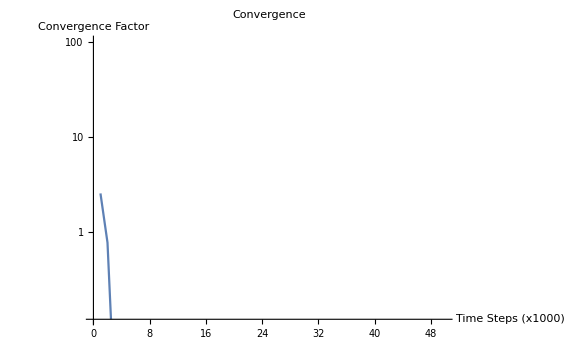

```mathematica
ListAnimate[ϕ3graph,ImageSize->Medium]
ListAnimate[ϕ4graph,ImageSize->Medium]
ListAnimate[ϕ5graph,ImageSize->Medium]

ListLogPlot[Q3,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence",PlotRange->{0,100}]

(*ListPlot[ϕ3Error,Joined->True,AxesLabel->{"Time Steps (x1000)","Error (Norm)"},PlotLabel->"Error with Exact Solution"]*)
```

```mathematica
Q3
```

{62.3715,71.0962,83.3704,81.0092,66.7732,53.6682,51.8982,49.177,48.91,53.8787,56.5918,59.9217,60.4802,62.3758,63.6541,63.3221,61.718,61.0722,60.0878,59.8481,59.8039,60.8965,61.5556,61.3717,60.5443,60.082,58.9376,58.6226,58.6215,59.0649,59.9061,60.7062,61.8846,62.724,62.8908,62.6418,61.8968,61.2355,60.7013,60.3305,60.5915,60.6726,60.8042,60.8602,60.8689,60.5856,60.4602,60.3198,60.4554,60.5614,61.0136,61.6717,62.2809,62.5607,62.6865,62.3959,61.9448,61.1061,60.6272,60.5335,60.4651,60.5828,60.7424,60.828,60.8741,60.9591,61.1298,61.1412,61.1022,61.2018,61.2082,61.2967,61.5055,61.7743,61.8227,61.7332,61.3842,61.0703,60.6479,60.2926,60.1761,60.3346,60.6187,61.0001,61.3316,61.5806,61.4771,61.309,61.0736,60.8278,60.604,60.5353,60.6708,60.8598,60.9859,60.9656,60.7098,60.3373,59.9517,59.7742}

### Saved Data

14.9903

15.39

15.1554

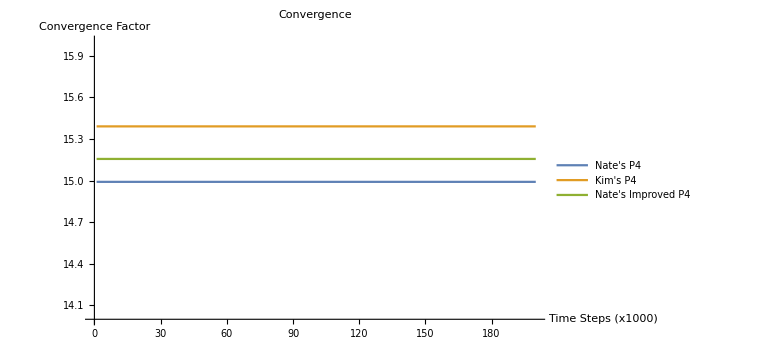

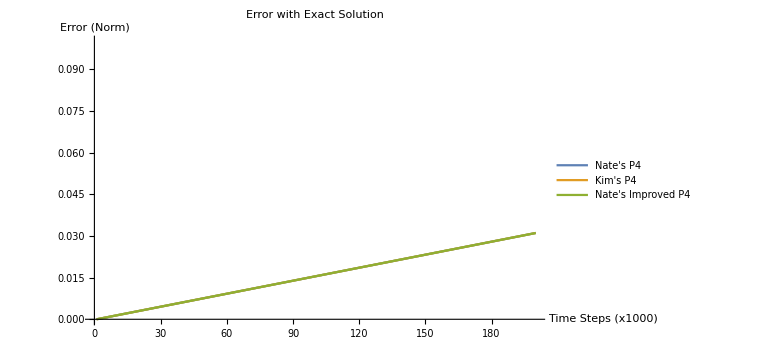

```mathematica
kim1Err={1.5605218774795745*^-7,0.00015620920345790632,0.00031226427997453556,0.00046832128175723013,0.0006243802088214108,0.000780441061203541,0.0009365038389173213,0.0010925685419925406,0.0012486351704492217,0.0014047037243141902,0.0015607742036076438,0.0017168466083563854,0.0018729209385819252,0.0020289971943149993,0.002185075375574027,0.002341155482371665,0.0024972375147477603,0.00265332147271909,0.0028094073563125132,0.0029654951655475876,0.003121584900461798,0.0032776765610612922,0.0034337701473743034,0.0035898656594336607,0.0037459630972504596,0.003902062460853727,0.004058163750268622,0.00421426696551665,0.004370372106628971,0.004526479173621928,0.004682588166517308,0.004838699085342272,0.00499481193011763,0.005150926700872681,0.005307043397629235,0.005463162020408745,0.005619282569238641,0.005775405044142774,0.005931529445145955,0.006087655772259145,0.006243784025524633,0.006399914204953932,0.006556046310577284,0.006712180342409847,0.006868316300477868,0.007024454184810973,0.007180593995433582,0.007336735732365348,0.007492879395631743,0.007649024985253486,0.00780517250125711,0.00796132194366435,0.008117473312499927,0.00827362660779023,0.008429781829556497,0.008585938977822841,0.008742098052612706,0.008898259053952525,0.009054421981860137,0.009210586836360713,0.009366753617483417,0.009522922325248815,0.00967909295968215,0.009835265520800317,0.00999144000863065,0.010147616423197408,0.010303794764530595,0.010459975032646625,0.010616157227574762,0.010772341349334134,0.010928527397950956,0.011084715373448704,0.011240905275846959,0.011397097105176364,0.01155329086145122,0.011709486544704696,0.011865684154955296,0.012021883692229991,0.012178085156550538,0.012334288547944364,0.012490493866430261,0.012646701112037117,0.01280291028478104,0.012959121384693665,0.013115334411793255,0.01327154936610626,0.013427766247662088,0.013583985056471282,0.013740205792567444,0.013896428455972437,0.01405265304671051,0.014208879564799442,0.014365108010272232,0.014521338383145626,0.014677570683445945,0.014833804911197833,0.014990041066424096,0.015146279149150677,0.015302519159398216,0.015458761097190847,0.015615004962553929,0.01577125075551001,0.01592749847608609,0.016083748124299874,0.016239999700179482,0.01639625320374838,0.016552508635028232,0.016708765994045666,0.016865025280821493,0.01702128649538416,0.017177549637750002,0.017333814707949074,0.017490081706002483,0.017646350631933146,0.017802621485767882,0.017958894267530067,0.01811516897723923,0.01827144561492548,0.01842772418061051,0.018584004674314928,0.01874028709606383,0.018896571445883675,0.019052857723794333,0.01920914592982515,0.019365436063992512,0.019521728126326642,0.01967802211684888,0.01983431803558293,0.01999061588255362,0.020146915657783936,0.02030321736129616,0.02045952099311709,0.02061582655326936,0.020772134041774054,0.020928443458655743,0.021084754803941865,0.021241068077653684,0.02139738327981566,0.021553700410452042,0.021710019469586894,0.021866340457241965,0.02202266337344305,0.022178988218213635,0.022335314991573818,0.0224916436935509,0.02264797432416718,0.022804306883448276,0.02296064137141589,0.023116977788095593,0.023273316133512335,0.023429656407688796,0.023585998610644355,0.023742342742408457,0.0238986888030052,0.024055036792452748,0.024211386710780294,0.02436773855800993,0.02452409233416327,0.02468044803926655,0.024836805673343947,0.024993165236416467,0.025149526728510476,0.025305890149650234,0.025462255499858415,0.025618622779160376,0.02577499198757932,0.02593136312513581,0.026087736191854175,0.026244111187763305,0.02640048811288367,0.02655686696723748,0.026713247750851,0.026869630463745187,0.027026015105948598,0.027182401677482315,0.027338790178367132,0.02749518060863222,0.027651572968299894,0.027807967257390456,0.02796436347592909,0.028120761623941743,0.028277161701454393,0.028433563708484547,0.028589967645061033,0.028746373511205313,0.028902781306944167,0.029059191032296216,0.029215602687288574,0.029372016271943798,0.02952843178628587,0.02968484923034049,0.029841268604127977,0.02999768990767714,0.03015411314100632,0.030310538304141193,0.030466965397108397,0.030623394419929215,0.03077982537262995,0.030936258255227448,0.031092693067754387};

kim1={15.390047473739987,15.390047257622196,15.390047350198888,15.390047280161703,15.390047280867547,15.390047333213033,15.390047338558775,15.390047315932119,15.390047307765764,15.390047366135404,15.390047321529169,15.39004731661853,15.390047343059921,15.390047327024295,15.390047325197896,15.390047342431544,15.39004734065273,15.390047317701175,15.390047339363544,15.39004734553793,15.39004733238464,15.39004734688555,15.390047355372953,15.390047337478489,15.390047349702662,15.390047368239191,15.390047345849508,15.390047362020582,15.390047373815237,15.390047352112997,15.390047369710658,15.390047380385571,15.390047360403807,15.390047368768833,15.390047389948615,15.390047373601124,15.39004736601888,15.39004739376085,15.390047377355929,15.390047372564792,15.390047397972499,15.390047380971307,15.390047382442667,15.390047394175456,15.39004739366477,15.39004738382462,15.390047394825935,15.39004740859026,15.39004738587346,15.390047399327203,15.390047419006963,15.390047389232029,15.390047413830212,15.390047420446708,15.390047401651147,15.39004741677394,15.390047423395142,15.39004741890814,15.39004741281167,15.3900474344967,15.390047427949787,15.390047413838042,15.39004744221811,15.390047434747876,15.390047420196991,15.390047442568253,15.390047442727068,15.390047430577617,15.390047441607273,15.390047451488167,15.390047439329845,15.390047442392136,15.3900474579934,15.390047444200723,15.390047444252987,15.390047466443527,15.390047452307243,15.39004745169956,15.390047470303227,15.390047462524581,15.390047455670848,15.390047471404294,15.390047473000271,15.39004745921859,15.390047473819351,15.390047481999293,15.390047465905019,15.390047478478193,15.390047487461562,15.390047475078944,15.390047480814056,15.390047494733196,15.390047483851097,15.39004748377526,15.39004750232892,15.390047490201551,15.390047488928882,15.390047506678222,15.390047498116342,15.390047496041857,15.390047508287916,15.390047508301123,15.390047500377422,15.390047511634512,15.39004751711599,15.390047504539982,15.39004751601261,15.390047525369628,15.390047510048904,15.390047522190667,15.390047529247806,15.390047518591038,15.390047525755657,15.390047534476567,15.390047530746239,15.390047525744995,15.390047542991852,15.390047537539202,15.39004752754756,15.390047551813879,15.39004754256832,15.390047534056713,15.390047555767786,15.390047547540206,15.390047544342037,15.390047553428463,15.390047558303335,15.390047551594586,15.390047553962777,15.390047568438156,15.390047553664923,15.390047557667158,15.390047576100581,15.390047557695128,15.390047566267244,15.390047576885816,15.39004756660675,15.390047571252682,15.39004757673386,15.390047579279543,15.390047572231042,15.390047581865717,15.390047589824771,15.390047573242493,15.390047589806587,15.390047593455012,15.390047579095306,15.390047596129907,15.390047595448209,15.390047589365834,15.390047597386456,15.390047601804406,15.390047598743173,15.39004759692549,15.390047609911994,15.390047604026792,15.390047599699617,15.390047617712721,15.390047609177065,15.390047605728709,15.39004762049239,15.390047616787616,15.39004761099445,15.39004762266242,15.390047625344968,15.390047616300107,15.390047624904124,15.390047632079948,15.390047621067694,15.390047628551836,15.390047636475769,15.390047627742998,15.390047631363043,15.390047641450957,15.390047634172108,15.390047633608587,15.390047647368876,15.390047639463022,15.390047637575046,15.39004765262656,15.390047644475512,15.390047643478173,15.390047654680659,15.390047651670434,15.39004764881212,15.390047656163778,15.390047661544335,15.390047651969041,15.390047660060313,15.390047669358143,15.390047655449614,15.390047666552281,15.390047672679692,15.390047661003006,15.390047671215262,15.390047674284641,15.390047671059593,15.390047671212104,15.3900476786204,15.39004767992253};

nate1Err={1.5605857422413267*^-7,0.0001562155964442274,0.0003122770596303659,0.0004683404481647305,0.0006244057620715288,0.0007804730013608499,0.0009365421660761795,0.0010926132562281425,0.0012486862718487186,0.0014047612129555246,0.001560838079575976,0.0017169168717349954,0.0018729975894469367,0.002029080232742472,0.0021851648016485694,0.0023412512961793353,0.002497339716369957,0.0026534300622405777,0.0028095223338150846,0.0029656165311120926,0.0031217126541600517,0.003277810702982739,0.0034339106775960844,0.0035900125780338023,0.0037461164043184943,0.0039022221564710222,0.004058329834507339,0.004214439438463408,0.004370550968363096,0.004526664424230343,0.004682779806075461,0.004838897113933054,0.004995016347829466,0.005151137507784164,0.005307260593820029,0.005463385605962283,0.005619512544232303,0.005775641408657836,0.005931772199254468,0.006087904916054389,0.006244039559075637,0.006400176128352315,0.006556314623895939,0.006712455045737695,0.006868597393902987,0.007024741668408701,0.007180887869277355,0.007337035996546101,0.007493186050228658,0.007649338030345212,0.007805491936929277,0.007961647769992608,0.008117805529569921,0.008273965215681196,0.008430126828347389,0.008586290367599026,0.008742455833451925,0.008898623225940497,0.00905479254507376,0.009210963790879476,0.009367136963395268,0.009523312062627812,0.009679489088617647,0.009835668041375608,0.009991848920927672,0.010148031727298747,0.010304216460509812,0.010460403120590234,0.010616591707560965,0.01077278222144081,0.01092897466226207,0.011085169030041283,0.011241365324802901,0.01139756354658005,0.01155376369538767,0.011709965771251595,0.011866169774198528,0.01202237570425146,0.012178583561428345,0.012334793345754064,0.012491005057255146,0.012647218695963237,0.012803434261889339,0.012959651755064175,0.013115871175511065,0.013272092523248083,0.013428315798306297,0.013584541000703377,0.013740768130466282,0.01389699718762233,0.014053228172189774,0.014209461084194587,0.014365695923661562,0.014521932690612395,0.01467817138506899,0.014834412007059598,0.01499065455660872,0.015146899033736594,0.015303145438466304,0.015459393770826179,0.015615644030834087,0.015771896218520008,0.01592815033390259,0.016084406377008423,0.016240664347860992,0.016396924246482262,0.016553186072898022,0.016709449827129356,0.016865715509202267,0.017021983119143554,0.017178252656970896,0.017334524122713836,0.017490797516391564,0.01764707283803066,0.017803350087655514,0.01795962926528487,0.018115910370949045,0.018272193404663656,0.018428478366461026,0.018584765256360214,0.01874105407438473,0.018897344820562597,0.01905363749491209,0.019209932097462867,0.019366228628233294,0.019522527087249154,0.019678827474536163,0.01983512979011769,0.019991434034014887,0.020147740206253734,0.02030404830685586,0.02046035833584612,0.0206166702932449,0.020772984179083468,0.02092929999338108,0.021085617736161372,0.02124193740744998,0.021398259007268577,0.021554582535642353,0.021710907992597332,0.021867235378154107,0.02202356469233898,0.022179895935169835,0.02233622910667837,0.022492564206886737,0.022648901235814627,0.022805240193488185,0.02296158107992695,0.023117923895161513,0.023274268639211074,0.02343061531210088,0.023586963913856777,0.023743314444499806,0.023899666904054588,0.024056021292546935,0.02421237760999748,0.02436873585643274,0.024525096031874097,0.02468145813634609,0.024837822169872983,0.02499418813247498,0.025150556024183684,0.025306925845019427,0.02546329759500386,0.025619671274161822,0.025776046882515835,0.025932424420094875,0.02608880388691633,0.026245185283004988,0.026401568608386983,0.02655795386308455,0.026714341047122468,0.026870730160526417,0.0270271212033178,0.027183514175519154,0.02733990907715689,0.027496305908255,0.02765270466883511,0.02780910535892321,0.02796550797853975,0.028121912527713098,0.02827831900646686,0.028434727414821104,0.0285911377528009,0.02874755002042713,0.028903964217728725,0.029060380344730366,0.029216798401451145,0.029373218387917416,0.029529640304152078,0.029686064150177976,0.02984248992602128,0.029998917631702902,0.030155347267247865,0.03031177883268333,0.030468212328029185,0.03062464775331335,0.030781085108553253,0.03093752439378147,0.03109396560901188};

nate1={14.990281607748729,14.990294862234729,14.99029482000456,14.990294598000569,14.990294815691291,14.99029489344153,14.990294648543914,14.990294696112146,14.990294803774114,14.990294792550854,14.990294666081978,14.990294611679571,14.99029487078368,14.99029467455468,14.99029452646619,14.990294861964887,14.990294721726467,14.990294651538612,14.9902947427994,14.990294799848579,14.99029475772122,14.99029462713856,14.990294858205797,14.990294761749864,14.990294662717146,14.99029479236849,14.990294755165161,14.990294757951714,14.990294708387626,14.990294764518982,14.990294825219939,14.990294652802195,14.990294775359315,14.990294824682346,14.990294705419132,14.990294729639185,14.990294755502294,14.990294779653334,14.9902946878747,14.990294771386454,14.990294811351657,14.990294681236628,14.990294781380664,14.99029476574776,14.990294720570388,14.990294786423897,14.990294713815507,14.990294765887667,14.990294759469526,14.990294723462945,14.99029477122862,14.990294738262147,14.99029475915336,14.990294719674432,14.990294746427258,14.99029476024437,14.990294691972236,14.99029478809567,14.99029474117109,14.99029471860809,14.99029479194223,14.990294724824391,14.990294770757622,14.990294756933242,14.990294736878342,14.990294785210152,14.990294737642436,14.99029476975806,14.990294744058149,14.990294762127075,14.990294769783464,14.990294721619566,14.990294796102996,14.990294731178766,14.990294747785484,14.990294799170908,14.990294710944564,14.990294781114033,14.990294774700708,14.990294737120973,14.990294777079642,14.990294759118555,14.990294783526402,14.990294744989104,14.990294783397497,14.990294784396774,14.990294732854856,14.990294810416293,14.990294752680635,14.990294761657232,14.990294804937397,14.990294740837102,14.990294793919954,14.990294773940828,14.990294765308501,14.990294808004007,14.990294761897323,14.990294790246347,14.99029478148488,14.990294791925091,14.990294788412667,14.990294756734205,14.990294828277511,14.990294758285842,14.990294770660585,14.990294829556214,14.990294751347738,14.990294800613421,14.990294796019032,14.990294779567856,14.990294808760053,14.990294771072165,14.99029481433513,14.990294784806034,14.990294787171049,14.99029481082646,14.990294773265084,14.990294817468715,14.990294775786465,14.990294795350788,14.990294822668215,14.990294748361887,14.990294827121808,14.9902947998158,14.99029476676344,14.990294820174338,14.990294793543864,14.990294803737552,14.990294781280124,14.990294811109818,14.990294817970106,14.990294762663883,14.990294833457874,14.990294796261464,14.990294796270122,14.990294822453983,14.990294773642363,14.990294837575227,14.99029479499898,14.990294786591946,14.990294846367604,14.99029479277453,14.990294807178536,14.990294812355115,14.99029482642708,14.990294807552496,14.99029478285583,14.990294864521612,14.990294791685146,14.990294795523361,14.990294856725386,14.990294794387346,14.99029482436113,14.99029481407648,14.99029482337893,14.990294835273959,14.990294785012848,14.99029484912083,14.990294822646128,14.990294803259479,14.990294831834385,14.99029481846411,14.990294847876614,14.990294787404284,14.990294834163521,14.990294869914383,14.990294775424816,14.990294849251704,14.990294849203114,14.990294813546715,14.990294838362413,14.990294821963882,14.990294862218112,14.990294811789747,14.990294827428965,14.9902948719517,14.99029480700889,14.990294846090656,14.990294835602684,14.990294845722648,14.990294850178518,14.990294797864518,14.99029488662273,14.990294831871449,14.990294802799745,14.990294883944864,14.990294831810093,14.99029483373044,14.990294836998682,14.99029486101973,14.990294850742108,14.99029480352753,14.990294891141621,14.990294837889262,14.990294818842184,14.990294879466497,14.990294831865539,14.990294862752842,14.990294831836849,14.990294850595353};

nateBetterErr={1.5605216309465687*^-7,0.0001562091787703103,0.00031226423061382836,0.0004683212077196217,0.0006243801101188549,0.0007804409378257191,0.0009365036908742667,0.0010925683692799178,0.0012486349730677906,0.0014047035022585921,0.0015607739568856292,0.0017168463369652825,0.0018729206425276315,0.0020289968735838775,0.0021850750301626214,0.002341155112295559,0.0024972371199963295,0.0026533210532979326,0.0028094069122173593,0.0029654946967860984,0.0031215844070242352,0.0032776760429515817,0.0034337696045910714,0.003589865091971768,0.0037459625051152823,0.003902061844042104,0.004058163108784668,0.0042142662993601655,0.004370371415790605,0.004526478458109844,0.004682587426327877,0.004838698320475194,0.004994811140572554,0.005150925886646736,0.005307042558723889,0.005463161156825265,0.00561928168097677,0.0057754041311997555,0.005931528507519065,0.006087654809954968,0.006243783038538601,0.006399913193285118,0.006556045274219139,0.006712179281370322,0.006868315214757749,0.007024453074407157,0.007180592860344725,0.0073367345725862685,0.00749287821116334,0.007649023776100168,0.007805171267412067,0.007961320685133982,0.008117472029285517,0.008273625299887885,0.008429780496967331,0.008585937620544609,0.0087420966706419,0.008898257647287515,0.00905442055050271,0.009210585380316568,0.009366752136743388,0.009522920819814715,0.009679091429553319,0.009835263965979522,0.009991438429120692,0.010147614819000138,0.0103037931356398,0.010459973379061401,0.010616155549297604,0.01077233964636474,0.010928525670288763,0.011084713621091155,0.01124090349879126,0.011397095303424101,0.011553289035009826,0.011709484693570305,0.011865682279123858,0.012021881791703604,0.01217808323133257,0.012334286598027643,0.012490491891816821,0.01264669911272368,0.012802908260770796,0.012959119335986456,0.013115332338390889,0.013271547268008303,0.013427764124858965,0.013583982908970593,0.013740203620368329,0.013896426259071623,0.014052650825108617,0.014208877318499713,0.014365105739268538,0.014521336087439263,0.014677568363035758,0.014833802566084527,0.014990038696607809,0.01514627675462777,0.01530251674017106,0.01545875865326196,0.015615002493921889,0.015771248262173302,0.015927495958042836,0.01608374558155268,0.016239997132728504,0.01639625061159082,0.016552506018164083,0.016708763352474308,0.01686502261454408,0.017021283804394535,0.017177546922053904,0.017333811967545642,0.017490078940889327,0.017646347842114503,0.017802618671240566,0.017958891428291456,0.01811516611329174,0.01827144272626627,0.018427721267241376,0.018584001736235367,0.018740284133276133,0.01889656845838602,0.01905285471158548,0.01920914289290329,0.019365433002359808,0.019521725039981307,0.019678019005790547,0.019834314899811276,0.01999061272206876,0.02014691247258211,0.020303214151381848,0.02045951775848678,0.020615823293921417,0.02077213075771136,0.02092844014987631,0.021084751470444873,0.021241064719436233,0.02139737989687893,0.021553697002797113,0.021710016037209175,0.021866337000144915,0.022022659891627404,0.022178984711673545,0.022335311460314436,0.02249164013757314,0.022647970743467524,0.02280430327802639,0.022960637741271328,0.023116974133227847,0.02327331245391933,0.02342965270336732,0.02358599488160014,0.023742338988639967,0.023898685024508367,0.024055032989232634,0.024211382882835298,0.02436773470533599,0.024524088456763796,0.024680444137140375,0.02483680174648953,0.02499316128483877,0.02514952275220713,0.02530588614861873,0.025462251474095927,0.025618618728668306,0.025774987912355423,0.025931359025182992,0.026087732067173446,0.026244107038351713,0.02640048393873769,0.02655686276836234,0.02671324352724354,0.026869626215405062,0.027026010832876837,0.02718239737967671,0.027338785855828024,0.02749517626135753,0.027651568596288985,0.027807962860644735,0.027964359054449568,0.02812075717772882,0.02827715723050528,0.02843355921280053,0.028589963124640957,0.028746368966049603,0.028902776737051248,0.029059186437668427,0.029215598067924706,0.029372011627841855,0.02952842711744522,0.02968484453675941,0.02984126388580725,0.029997685164614613,0.030154108373203932,0.030310533511598944,0.03046696057982256,0.030623389577901863,0.03077982050585635,0.03093625336371522,0.031092688151494824};

nateBetter={15.155448968593014,15.155438680799355,15.1554386190513,15.155438591807885,15.155438700421529,15.155438659917229,15.155438663265851,15.155438646381345,15.155438685353882,15.155438643389564,15.15543864146038,15.1554387051732,15.155438641971433,15.155438679175278,15.155438691887499,15.155438679787165,15.155438708726122,15.155438671253934,15.155438703941988,15.155438708943231,15.155438691920253,15.155438724904961,15.155438701855468,15.155438703237323,15.155438736537384,15.155438690766404,15.155438726298314,15.15543870403243,15.155438704743245,15.155438713872055,15.155438696148394,15.155438711251444,15.15543870106434,15.155438720428217,15.155438705776698,15.155438695516409,15.155438736079489,15.155438697457786,15.155438709113623,15.155438729754653,15.155438710424031,15.15543870556894,15.155438718701824,15.15543872833456,15.15543871230295,15.155438715981534,15.15543873517671,15.155438715274927,15.15543871306623,15.155438738497502,15.155438726929862,15.1554387187096,15.155438732644841,15.155438740302644,15.15543872556513,15.15543872494813,15.15543874750597,15.155438736341846,15.155438728322478,15.15543874487401,15.155438744382648,15.1554387296964,15.155438741167776,15.155438759639992,15.155438735326978,15.155438740506648,15.155438763702293,15.15543874366176,15.155438744822373,15.155438761143227,15.155438755540898,15.155438741944387,15.155438752519284,15.155438768268782,15.155438747724363,15.155438754956675,15.155438774487976,15.155438754210262,15.155438757685516,15.155438775587493,15.155438770453378,15.15543875832448,15.155438772705159,15.155438784643035,15.155438756963765,15.15543877067315,15.155438792241004,15.15543876437827,15.155438773636291,15.155438788551727,15.155438776878201,15.155438770336136,15.155438782988265,15.155438793198075,15.155438768265036,15.155438780102958,15.155438800799166,15.155438770321764,15.15543878254109,15.155438801310037,15.155438780797244,15.155438781774954,15.155438800652668,15.155438796836929,15.155438779164522,15.155438797794556,15.155438807608757,15.1554387826531,15.155438798102251,15.155438810903537,15.155438789292875,15.155438795895305,15.155438809135449,15.155438800483225,15.15543879243184,15.155438806772809,15.155438814873591,15.15543879259185,15.155438808375965,15.155438823314276,15.155438800124475,15.155438805038257,15.155438823167465,15.155438814813426,15.155438803163209,15.155438821503061,15.155438829028725,15.155438803256025,15.155438820593501,15.155438835255026,15.155438808466384,15.155438821213451,15.15543883649289,15.155438820702363,15.155438816987619,15.15543883304242,15.15543883523071,15.155438813841162,15.155438833083311,15.155438843533924,15.155438818911247,15.155438830312375,15.155438845368733,15.155438829780197,15.155438826318319,15.155438848274292,15.155438842003118,15.155438822812016,15.155438847743987,15.155438849421454,15.155438827195317,15.155438846673972,15.15543885241316,15.15543883693173,15.155438841719198,15.15543885637786,15.15543884973494,15.155438836690324,15.155438860311623,15.15543885836656,15.1554388371008,15.155438860733303,15.155438864687078,15.15543884458826,15.155438856237316,15.15543886963034,15.155438854533632,15.155438849936484,15.155438873405828,15.15543886430032,15.155438848429272,15.155438875398145,15.155438871972747,15.155438853598257,15.155438869859278,15.15543887968013,15.155438864078835,15.155438862067527,15.15543888784434,15.15543887465925,15.155438857860819,15.155438889974707,15.155438883746445,15.1554388619621,15.15543888476202,15.155438891938688,15.155438871109471,15.15543887578886,15.155438899757835,15.155438881675108,15.1554388705586,15.15543890221166,15.15543889109468,15.155438873125677,15.1554388966997,15.155438900099805,15.155438880945324,15.155438887597345,15.155438909191034,15.155438889128447};

Mean[nate1]
Mean[kim1]
Mean[nateBetter]

ListPlot[{nate1,kim1,nateBetter},Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence",PlotRange->{14,16},PlotLegends->{"Nate's P4","Kim's P4","Nate's Improved P4"}]

ListPlot[{nate1Err,kim1Err,nateBetterErr},Joined->True,AxesLabel->{"Time Steps (x1000)","Error (Norm)"},ImageSize->Large,PlotLabel->"Error with Exact Solution",PlotRange->{0,0.1},PlotLegends->{"Nate's P4","Kim's P4","Nate's Improved P4"}]
```

4.06511

4.07379

4.06951

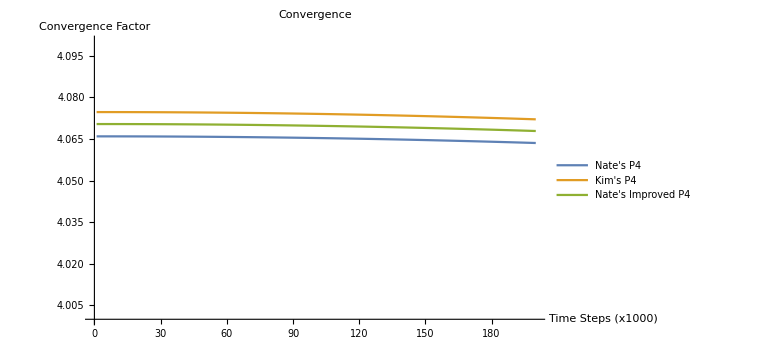

4.03037

4.07421

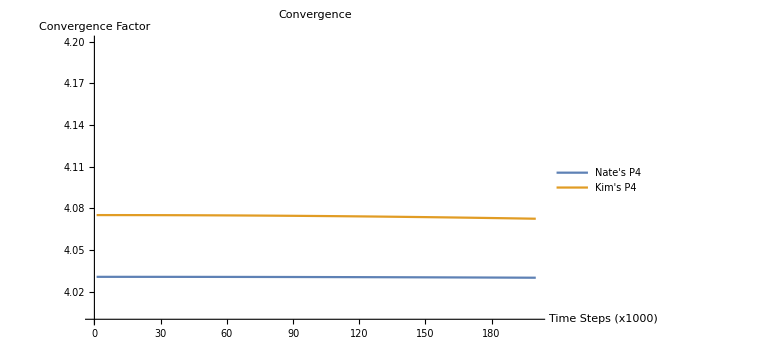

```mathematica
(* Incorrect Data *)
nateBetter={4.070343127862542,4.0703431619915635,4.070343069014884,4.070342848374648,4.070342500076757,4.070342024122939,4.0703414205459945,4.070340689312026,4.070339830414648,4.070338843878047,4.07033772969652,4.070336487864103,4.070335118383532,4.070333621252482,4.070331996473572,4.070330244044605,4.070328363967529,4.070326356245862,4.0703242208729815,4.0703219578527365,4.070319567185308,4.0703170488665235,4.070314402900535,4.070311629295909,4.070308728035589,4.070305699126575,4.070302542573225,4.0702992583722155,4.070295846526446,4.070292307035061,4.070288639896207,4.070284845100695,4.070280922671346,4.070276872597338,4.070272694872873,4.070268389504985,4.070263956485744,4.070259395823419,4.0702547075226585,4.07024989157747,4.070244947981366,4.070239876739459,4.070234677859051,4.070229351335189,4.070223897169631,4.070218315360368,4.070212605900248,4.070206768801736,4.070200804070012,4.0701947116897195,4.070188491667485,4.070182144001028,4.070175668697699,4.070169065756915,4.070162335171995,4.070155476948528,4.070148491080363,4.070141377577934,4.070134136438122,4.070126767658142,4.070119271240139,4.070111647180706,4.0701038954885504,4.070096016159818,4.0700880091919585,4.070079874591249,4.070071612350417,4.070063222478391,4.070054704971875,4.070046059826128,4.070037287051456,4.070028386641883,4.070019358598835,4.070010202921931,4.0700009196136895,4.069991508676383,4.069981970104406,4.069972303906449,4.06996251007344,4.069952588608716,4.069942539523319,4.069932362805043,4.0699220584577045,4.0699116264826465,4.069901066878697,4.069890379653185,4.0698795648011,4.069868622323302,4.069857552214418,4.069846354485529,4.069835029137463,4.069823576160979,4.069811995565397,4.069800287342848,4.0697884514987805,4.069776488041841,4.069764396961122,4.069752178258848,4.069739831936183,4.069727357998072,4.069714756443882,4.069702027270569,4.069689170483607,4.069676186075429,4.069663074054341,4.0696498344243075,4.069636467175683,4.069622972314337,4.069609349841132,4.069595599756596,4.069581722061712,4.069567716756689,4.069553583842955,4.069539323316256,4.069524935186479,4.069510419449029,4.069495776101534,4.0694810051528725,4.069466106596615,4.069451080435713,4.069435926673415,4.069420645306402,4.0694052363386435,4.069389699770496,4.069374035602188,4.069358243831431,4.069342324462856,4.069326277500897,4.069310102938007,4.0692938007795965,4.06927737102563,4.06926081367496,4.069244128735352,4.069227316203126,4.069210376075005,4.069193308355085,4.069176113048062,4.069158790152279,4.069141339667067,4.069123761595068,4.069106055932432,4.069088222685859,4.069070261859543,4.069052173445582,4.069033957447557,4.069015613867985,4.068997142706789,4.068978543968258,4.068959817650679,4.068940963752579,4.068921982275513,4.068902873225439,4.068883636600773,4.068864272399887,4.0688447806270895,4.068825161279307,4.06880541436148,4.068785539876551,4.0687655378191305,4.068745408193978,4.068725151002177,4.068704766243457,4.06868425392074,4.068663614033668,4.068642846583786,4.0686219515708215,4.068600928998619,4.068579778866068,4.068558501173349,4.068537095926056,4.068515563121325,4.068493902759695,4.068472114844506,4.0684501993762225,4.068428156356835,4.068405985786961,4.068383687666678,4.068361261995273,4.068338708778346,4.068316028018106,4.068293219709911,4.068270283858131,4.06824722046281,4.068224029524943,4.06820071105093,4.068177265036728,4.068153691481705,4.068129990390254,4.068106161764317,4.068082205605343,4.068058121913077,4.068033910688455,4.068009571930599,4.067985105645343,4.067960511835128,4.067935790495036,4.067910941629558,4.067885965239491,4.067860861325949,4.067835629893247};

kim2={4.075080431220267,4.075080465065016,4.07508036455517,4.075080130610896,4.075079763192823,4.075079262289761,4.075078627954009,4.075077860122211,4.075076958839879,4.07507592408052,4.075074755853568,4.0750734541731095,4.075072019022607,4.0750704503922615,4.075068748309162,4.075066912750499,4.075064943734844,4.075062841252809,4.07506060529042,4.075058235876417,4.0750557329903465,4.075053096643523,4.075050326830729,4.075047423542253,4.075044386799628,4.075041216586749,4.075037912912997,4.075034475773405,4.075030905160887,4.075027201094951,4.0750233635621145,4.075019392562128,4.0750152881019215,4.075011050171511,4.07500667878502,4.0750021739371896,4.0749975356175945,4.074992763841166,4.074987858598674,4.074982819896274,4.0749776477359,4.074972342107227,4.074966903020974,4.074961330470348,4.074955624460415,4.074949784995119,4.074943812063421,4.074937705672872,4.074931465824488,4.0749250925148734,4.074918585751805,4.074911945523209,4.074905171840522,4.074898264698932,4.07489122410059,4.0748840500457195,4.074876742533497,4.07486930156244,4.07486172714159,4.074854019260899,4.074846177926418,4.074838203138137,4.074830094891212,4.074821853195297,4.074813478046662,4.07480496944074,4.074796327386639,4.074787551876617,4.074778642917918,4.074769600509828,4.0747604246460485,4.074751115336269,4.074741672575722,4.074732096364115,4.074722386710258,4.074712543601519,4.074702567048026,4.074692457048572,4.074682213599114,4.074671836710114,4.074661326371566,4.074650682586943,4.074639905362314,4.0746289946890215,4.074617950577426,4.074606773023306,4.074595462022509,4.074584017586608,4.074572439704692,4.074560728385203,4.074548883629343,4.07453690542887,4.074524793795051,4.074512548721531,4.0745001702096735,4.074487658267662,4.074475012883639,4.074462234068875,4.074449321818522,4.0744362761324835,4.0744230970201,4.074409784470714,4.074396338490286,4.074382759081962,4.074369046238544,4.07435519997326,4.074341220276608,4.074327107149077,4.074312860600085,4.074298480619499,4.074283967217433,4.074269320392859,4.074254540138168,4.074239626466187,4.07422457936822,4.074209398849924,4.0741940849155736,4.07417863755473,4.074163056778803,4.074147342585046,4.074131494969965,4.074115513946368,4.074099399500416,4.074083151640805,4.074066770371086,4.074050255682839,4.074033607589362,4.074016826081292,4.073999911159904,4.073982862835918,4.073965681096868,4.073948365955366,4.073930917407389,4.073913335447877,4.0738956200909815,4.073877771325878,4.073859789158917,4.073841673593894,4.073823424621309,4.073805042253892,4.073786526487305,4.073767877319043,4.073749094760428,4.073730178799999,4.07371112944708,4.073691946702374,4.073672630559778,4.073653181031186,4.073633598109327,4.073613881795795,4.073594032098994,4.073574049008077,4.073553932536237,4.073533682678054,4.07351329943189,4.07349278280771,4.073472132796771,4.073451349407453,4.073430432640869,4.07340938248904,4.0733881989653415,4.073366882062011,4.0733454317832924,4.073323848135078,4.0733021311076545,4.073280280711528,4.073258296945267,4.073236179806184,4.073213929305156,4.07319154543119,4.07316902819244,4.073146377591933,4.073123593623414,4.073100676298064,4.073077625608356,4.073054441557081,4.07303112415271,4.07300767338547,4.07298408926643,4.072960371791917,4.072936520959645,4.072912536781694,4.0728884192484545,4.07286416836648,4.072839784139134,4.072815266558925,4.072790615638297,4.072765831371859,4.072740913759819,4.072715862811567,4.07269067851759,4.0726653608869015,4.072639909920684,4.072614325612536,4.072588607976034,4.072562757002526,4.0725367726958766,4.072510655062882,4.072484404094832,4.072458019803279};

nate2={4.030582718309845,4.03058275820232,4.030582765692835,4.0305827402387004,4.030582681757959,4.030582590301052,4.030582465865451,4.030582308480391,4.030582118122773,4.030581894776192,4.030581638433398,4.030581349110052,4.030581026826145,4.030580671582527,4.030580283360941,4.030579862145949,4.030579407948533,4.030578920774592,4.030578400632928,4.030577847516587,4.030577261420817,4.030576642345346,4.030575990300118,4.030575305283782,4.030574587283247,4.030573836293277,4.030573052326476,4.030572235395204,4.030571385497043,4.030570502619927,4.030569586756095,4.03056863790882,4.030567656088699,4.0305666412949135,4.030565593529418,4.030564512787802,4.030563399066605,4.030562252365838,4.030561072689033,4.030559860036502,4.030558614406911,4.030557335801901,4.030556024223716,4.030554679670456,4.0305533021367665,4.030551891622373,4.030550448131891,4.030548971668245,4.030547462230735,4.030545919817988,4.0305443444265965,4.030542736056714,4.030541094710119,4.030539420388052,4.030537713091644,4.030535972818864,4.030534199568094,4.030532393343031,4.030530554142028,4.030528681964717,4.03052677681013,4.030524838677154,4.030522867568568,4.030520863487997,4.03051882643226,4.030516756400124,4.030514653389161,4.030512517401058,4.030510348437418,4.030508146498783,4.030505911587084,4.030503643700584,4.030501342836579,4.03049900899474,4.030496642175993,4.0304942423817876,4.030491809613482,4.030489343872625,4.030486845156681,4.030484313463163,4.0304817487917655,4.0304791511435285,4.030476520520106,4.030473856923023,4.030471160352757,4.030468430809972,4.030465668290243,4.030462872791399,4.030460044314234,4.030457182861592,4.030454288438598,4.03045136104554,4.030448400677927,4.030445407329507,4.030442381000746,4.030439321697474,4.030436229424758,4.030433104180858,4.0304299459607895,4.030426754762034,4.030423530587551,4.030420273440931,4.030416983320629,4.030413660222671,4.030410304147692,4.030406915101456,4.0304034930867685,4.030400038097865,4.030396550128253,4.03039302917821,4.030389475256069,4.0303858883666095,4.0303822685068,4.030378615670021,4.030374929853432,4.030371211061775,4.0303674592999075,4.030363674566305,4.030359856855766,4.030356006168067,4.03035212250955,4.030348205882792,4.0303442562828575,4.030340273703084,4.030336258143872,4.030332209613211,4.030328128116169,4.0303240136498015,4.030319866207312,4.030315685784795,4.030311472387399,4.030307226020854,4.030302946684158,4.030298634373016,4.030294289085965,4.030289910827345,4.030285499598833,4.030281055397327,4.0302765782184125,4.030272068062999,4.030267524938473,4.030262948848189,4.030258339787419,4.030253697748367,4.0302490227301115,4.030244314739797,4.030239573782869,4.030234799858353,4.030229992959385,4.03022515308488,4.0302202802372875,4.030215374419585,4.030210435630843,4.030205463867716,4.030200459131626,4.030195421426341,4.030190350753857,4.030185247109553,4.0301801104886925,4.030174940892206,4.0301697383252515,4.0301645027922515,4.0301592342918005,4.030153932817776,4.030148598369055,4.030143230947609,4.030137830556839,4.0301323971971,4.030126930865955,4.030121431563234,4.030115899290842,4.030110334049934,4.030104735837765,4.030099104651786,4.030093440493373,4.030087743366176,4.0300820132725,4.030076250211113,4.030070454177683,4.030064625170418,4.030058763192216,4.030052868245098,4.030046940329822,4.030040979445956,4.030034985592643,4.030028958770402,4.030022898978252,4.030016806214923,4.030010680480331,4.030004521776218,4.0299983301055775,4.029992105469043,4.029985847864299,4.0299795572885895,4.029973233740193,4.029966877221866,4.029960487736319,4.0299540652848105,4.029947609867845,4.029941121482402};

kim1={4.0746567318715154,4.074656764671692,4.0746566648345635,4.074656432032462,4.074656066267252,4.074655567538165,4.074654935852119,4.074654171186738,4.0746532735636505,4.074652242981447,4.074651079423579,4.074649782912929,4.074648353434335,4.0746467909794974,4.0746450955740645,4.074643267204697,4.074641305862919,4.074639211563932,4.074636984294898,4.074634624063757,4.074632130878254,4.074629504721303,4.074626745603893,4.0746238535210555,4.07462082846982,4.074617670467768,4.0746143794987875,4.074610955563352,4.074607398666824,4.074603708807297,4.074599885988075,4.074595930211863,4.074591841463847,4.074587619762614,4.0745832650932865,4.0745787774665745,4.074574156883796,4.074569403335572,4.074564516826369,4.074559497360795,4.074554344928083,4.0745490595457,4.0745436412010285,4.074538089893596,4.074532405632947,4.074526588408369,4.074520638230309,4.074514555096049,4.0745083389981875,4.074501989949083,4.074495507940911,4.074488892975145,4.074482145060342,4.074475264180242,4.074468250351114,4.074461103567102,4.074453823824957,4.074446411133996,4.074438865485515,4.074431186883654,4.074423375332788,4.074415430825128,4.074407353367647,4.074399142959921,4.074390799595587,4.07438232328787,4.074373714025042,4.07436497181168,4.074356096654694,4.074347088542097,4.074337947485673,4.074328673481572,4.074319266523965,4.0743097266284956,4.074300053780628,4.074290247987681,4.074280309252663,4.074270237565701,4.074260032940798,4.07424969537308,4.074239224855315,4.074228621403677,4.074217885001043,4.074207015661868,4.074196013385147,4.074184878160715,4.074173610001605,4.074162208902185,4.07415067485983,4.074139007889957,4.07412720797306,4.074115275123201,4.074103209338964,4.0740910106136035,4.074078678961324,4.0740662143709825,4.074053616844101,4.074040886391623,4.0740280229998,4.074015026681039,4.074001897433105,4.073988635248412,4.073975240142879,4.0739617121025296,4.07394805113547,4.073934257245431,4.07392033042419,4.073906270679342,4.073892078011822,4.0738777524136704,4.073863293899691,4.073848702458928,4.073833978097059,4.073819120816468,4.0738041306111805,4.073789007488997,4.073773751451154,4.073758362489615,4.073742840617033,4.0737271858234,4.073711398115414,4.07369547749723,4.0736794239613365,4.073663237512868,4.073646918154708,4.073630465880989,4.07361388070388,4.073597162614395,4.073580311613728,4.073563327710123,4.07354621089543,4.073528961179737,4.073511578558958,4.073494063029678,4.073476414601875,4.073458633270827,4.073440719038041,4.073422671910137,4.073404491875367,4.073386178947568,4.073367733122224,4.0733491543990406,4.0733304427845125,4.07331159827232,4.073292620866077,4.073273510573087,4.073254267383509,4.073234891307889,4.0732153823422035,4.073195740485294,4.073175965746941,4.073156058119571,4.073136017606905,4.073115844214375,4.07309553793392,4.073075098775229,4.073054526737142,4.073033821814946,4.073012984020972,4.072992013345318,4.0729709097942655,4.0729496733710135,4.072928304070155,4.072906801899622,4.072885166858988,4.072863398942097,4.072841498162988,4.0728194645110545,4.072797297994778,4.072774998614716,4.072752566365414,4.072730001255696,4.072707303285441,4.072684472450765,4.072661508762349,4.072638412209425,4.072615182801067,4.0725918205403495,4.072568325420936,4.072544697451707,4.072520936628354,4.0724970429518805,4.072473016431616,4.072448857059208,4.072424564840626,4.072400139778633,4.072375581866715,4.072350891118108,4.072326067525643,4.072301111090842,4.072276021820567,4.072250799709354,4.072225444762644,4.072199956984741,4.072174336366721,4.072148582922181,4.072122696643912,4.072096677535786,4.072070525602651,4.072044240839771};

nate1={4.065908272289868,4.0659083084340875,4.065908222655283,4.06590801485884,4.065907685095766,4.065907233337191,4.065906659563333,4.065905963798246,4.065905146035727,4.0659042062648645,4.065903144499312,4.0659019607415425,4.065900654983291,4.065899227218285,4.065897677458844,4.065896005707697,4.065894211952834,4.065892296191559,4.065890258438403,4.0658880986924935,4.0658858169438865,4.06588341319435,4.065880887453728,4.065878239713563,4.065875469968965,4.06587257823186,4.065869564502267,4.065866428769476,4.0658631710354385,4.065859791313118,4.065856289596444,4.0658526658744805,4.065848920156389,4.0658450524473615,4.065841062739691,4.065836951036257,4.0658327173402915,4.065828361644283,4.065823883952136,4.065819284269291,4.065814562593982,4.065809718921004,4.065804753248922,4.065799665585169,4.0657944559338635,4.065789124286295,4.06578367064273,4.065778095006041,4.065772397375653,4.065766577755573,4.06576063614668,4.065754572541494,4.0657483869407764,4.065742079354374,4.065735649778548,4.06572909820887,4.065722424647666,4.065715629097569,4.065708711558815,4.065701672031543,4.065694510512752,4.0656872270062125,4.065679821511994,4.06567229402853,4.0656646445582645,4.0656568731013945,4.0656489796563715,4.06564096422552,4.065632826810623,4.065624567406555,4.065616186017204,4.065607682645786,4.065599057289783,4.065590309948748,4.065581440622329,4.065572449313217,4.065563336024405,4.065554100753423,4.065544743497775,4.065535264259802,4.065525663043414,4.065515939847064,4.065506094671253,4.065496127514597,4.065486038376662,4.065475827261553,4.065465494171378,4.065455039104144,4.065444462056497,4.065433763030375,4.065422942031664,4.06541199906094,4.065400934111296,4.065389747185936,4.065378438289877,4.065367007418619,4.065355454574594,4.06534377976295,4.065331982976503,4.065320064214848,4.0653080234877725,4.06529586079321,4.0652835761259585,4.0652711694892565,4.065258640885705,4.06524599031611,4.0652332177791735,4.065220323275044,4.065207306806728,4.065194168373663,4.065180907974255,4.065167525613354,4.065154021291208,4.065140395003109,4.065126646753846,4.065112776547771,4.065098784379121,4.065084670248319,4.065070434161622,4.065056076118112,4.06504159611505,4.065026994155236,4.065012270239546,4.064997424369523,4.064982456545319,4.064967366765675,4.064952155033827,4.064936821350466,4.064921365713468,4.0649057881281925,4.064890088594161,4.064874267105719,4.064858323669891,4.064842258291419,4.064826070963383,4.064809761686838,4.064793330467152,4.06477677730269,4.064760102194287,4.064743305144724,4.064726386151793,4.064709345216284,4.064692182341458,4.0646748975275715,4.0646574907762885,4.064639962085824,4.06462231145602,4.064604538893066,4.0645866443967416,4.064568627962217,4.064550489594698,4.0645322292970185,4.064513847065893,4.0644953429039505,4.064476716813813,4.064457968792958,4.064439098844307,4.064420106969595,4.064400993167938,4.064381757441602,4.0643623997904985,4.064342920215531,4.064323318720613,4.064303595303027,4.064283749962207,4.0642637827055195,4.064243693531164,4.064223482436014,4.0642031494256665,4.06418269450093,4.064162117659914,4.064141418907032,4.0641205982425195,4.06409965566379,4.064078591175442,4.064057404779274,4.064036096474351,4.064014666262206,4.063993114142557,4.0639714401175295,4.063949644190962,4.063927726360534,4.063905686626632,4.0638835249932965,4.0638612414592625,4.063838836026118,4.0638163086988035,4.063793659473063,4.063770888348813,4.06374799533356,4.063724980426441,4.06370184362533,4.063678584933826,4.063655204352283,4.063631701882111,4.063608077525989,4.0635843312827955,4.063560463153992,4.063536473142607,4.063512361247197};

Mean[nate1]
Mean[kim1]
Mean[nateBetter]

ListPlot[{nate1,kim1,nateBetter},Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence",PlotRange->{4,4.1},PlotLegends->{"Nate's P4","Kim's P4","Nate's Improved P4"}]


Mean[nate2]
Mean[kim2]

ListPlot[{nate2,kim2},Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence",PlotRange->{4,4.2},PlotLegends->{"Nate's P4","Kim's P4"}]
```

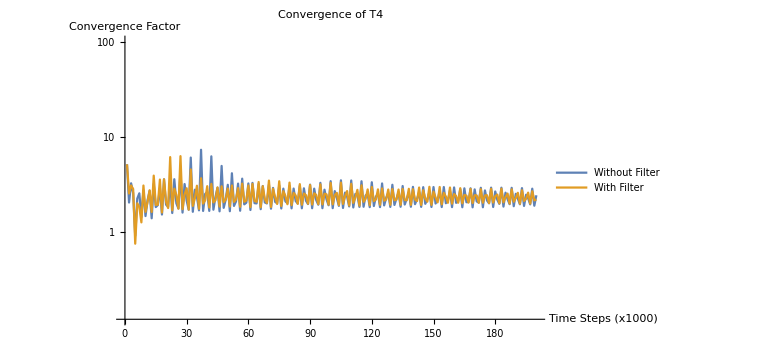

```mathematica
(* Without filtering *)
wf={5.186299741592986,2.0601087790917925,3.279252771772702,2.5925511091498485,0.9237715755894984,2.2664816141800634,2.5764103901519335,1.451941998632944,2.7668059145481125,1.4863874418860354,2.1782993775435195,2.7294228251739305,1.4085727108729602,3.229887312956899,1.8460166266383544,1.9377926314258642,2.928669113998219,1.5423344415172642,3.6114268809240766,1.9577416790179547,1.8569875470653696,3.3748292101624906,1.5998174869275077,3.618843153487784,2.021532728934619,1.7880251269483094,4.380504985337375,1.6162614332118135,3.22086514971744,2.1621801102300657,1.731631169084513,6.105388640545315,1.6476481070177993,2.8094224553242193,2.369286365985091,1.7072664008327905,7.368528969746697,1.6822425861496078,2.5389694809086847,2.641918142547688,1.6838291408896282,6.28799223814683,1.7328505494428124,2.3521897674931593,2.9445192564563034,1.6663789855454914,4.988099072216275,1.8123556902798967,2.2142610972152172,3.16298377931406,1.670827115284408,4.179607563505564,1.8978825896052411,2.117628527962366,3.2556715680457957,1.6899478678339117,3.6683580709876855,1.972457950957319,2.0508688207790913,3.2674894334324156,1.7209010581416349,3.3103042989121585,2.0287983588545977,2.0173490216929775,3.2313820075941226,1.7552048878952653,3.0705954635336195,2.06508178443167,2.0161484240451837,3.1741928618933604,1.775336840691931,2.934606329238125,2.0930062917256542,2.02489100558568,3.1131724818098183,1.784203427616719,2.8822765716727634,2.1190646218506397,2.026515092431686,3.0700354025765964,1.7898764240407299,2.8877847927177793,2.135966526956636,2.0124370006231174,3.084692958140951,1.7927996631054048,2.904680297363687,2.1518460035660274,1.9845007477479142,3.174621688984969,1.7954572873666927,2.8810183605376585,2.178775387300469,1.9553354874137026,3.314978453788366,1.79723679928366,2.809679082610326,2.224129419446191,1.9294119275771682,3.4528472498007985,1.7984603205871554,2.7160326900615472,2.2935952024566033,1.902105862557924,3.5247666667064395,1.8077842379106244,2.620475810113098,2.3789378801712586,1.875580066142584,3.509074694315747,1.829983832063085,2.532518625099789,2.458941231982569,1.8548029060179332,3.4447651497429392,1.8609294185379641,2.449179890037895,2.520743855887456,1.8437403951097102,3.363581390053185,1.8943826683179594,2.3707727156028815,2.5642342729244794,1.8450902131555615,3.268152958801148,1.923164853653276,2.3096939234674654,2.596563629293738,1.8537409482571947,3.1646776331727353,1.944519587190824,2.2734311042301223,2.6240318580677546,1.8602493936206246,3.0711844464543696,1.9627862505682707,2.2560853326768435,2.6432189091088203,1.8605109223224388,3.008323660992778,1.9805480752058628,2.2443796550777373,2.652608538830081,1.856008091544885,2.9874495642122527,1.996839808209307,2.224578341236978,2.6658750821075596,1.8508906928065156,2.9949862414133643,2.0115984120852155,2.1929149100290184,2.700098889196262,1.847765541146851,2.9969852076701544,2.025963338973217,2.156587180684181,2.761091673249055,1.8441227957141948,2.9665200207702718,2.0447149460727214,2.1215713418528237,2.8376749481002137,1.8386495300380543,2.9044174130040847,2.0746705108617634,2.0886406684284364,2.904599085543075,1.8354385837534586,2.8313072742198395,2.116522783953562,2.0562626811631404,2.9424311138956374,1.8388747204300375,2.760836573513823,2.1631031314365625,2.0239497819361056,2.9527290058969613,1.8504513445607411,2.6900074009408184,2.204410464024645,1.996525519153619,2.948835514962011,1.8677607594567385,2.615587891803079,2.2357925916747154,1.9802742278435734,2.9390253843177723,1.8853488751830385,2.5449965570317614,2.261719961093078,1.9746267826608044,2.9182993784642997,1.8983012524855583,2.4876771604465775,2.284136282755357,1.9691345095504524,2.879471458379159,1.907746809089903,2.4555105513421074};
(* with filtering *)
withF={5.187301107778856,2.562582952050685,3.1137215605197808,2.856908844639536,0.762763209385838,2.026612678208842,1.8517867630699443,1.2760769945456572,3.1079001981278944,1.6443399892932893,2.0894987999330823,2.7727021908076233,1.6421227802466045,3.94679628031921,1.943759498741464,1.957438138059403,3.5881093920843106,1.6212372156657193,3.6101141393268685,2.1062677122790374,1.804909163069974,6.173587482516589,1.7067555235793066,2.8777923593396113,2.4742622112014065,1.7746789972266632,6.318465440902977,1.754641134872297,2.494646351210193,2.9089170378797373,1.7361336258988684,4.583639936907376,1.9002323396650271,2.2853966193247324,3.0932175927183825,1.768605119811656,3.7044696179819345,2.0091972835464653,2.1742522687110215,3.059666466114895,1.827736475151969,3.232904445922312,2.066217660729136,2.1772428889388977,2.9707845197095177,1.8698507910834439,3.052260242496026,2.081460201178684,2.218525327738717,2.890328100706314,1.8701664421174107,3.109736784516523,2.090350053776652,2.2184917437907306,2.9157305400965146,1.8595267398578152,3.2516299111461464,2.0970196337521845,2.161225853172838,3.1126201254772434,1.8469873030427935,3.229803069506536,2.139444676915413,2.0975218200068357,3.3834351231359094,1.8374797829311351,3.0584373871876194,2.2382906319612714,2.038940030938122,3.502386382737726,1.8516820805265943,2.873361148536357,2.3481949318618542,1.9918942932739296,3.4456619172983047,1.8953621223322508,2.7145104939747617,2.4167085797707473,1.9791867677959654,3.3353129770527925,1.9356423705496901,2.5984058956513882,2.4478858036900117,1.9958760238034277,3.2150884442330687,1.9539875438566612,2.5606152847582844,2.4640983656180753,2.0010837824979317,3.1471837114088057,1.9638472102874374,2.571700571091834,2.4746353224534565,1.9828331501081062,3.195748975761658,1.9704264636036646,2.5494094480203935,2.5096942301101457,1.9609197678786097,3.308250958131592,1.9740415657775854,2.474787628508055,2.600769704419364,1.9394983986559224,3.33255785141133,1.9941995726852237,2.3947138728128436,2.720540123838231,1.917466056344156,3.241357314968109,2.041965983676305,2.3218138724201283,2.800504676459105,1.9127165897282576,3.1222520913281815,2.0960596179600564,2.2554544624698405,2.827303048067456,1.9312314660043584,3.0007093117987442,2.1321583467165177,2.219537564453664,2.8315129714942864,1.949418581095676,2.897094670688043,2.1553239890448532,2.2163389292283022,2.8219974468064337,1.9515548077171945,2.8553960348257115,2.1747809957798427,2.2075556017179463,2.82087568732684,1.949834050982265,2.8647777850656704,2.189340970089989,2.1740707591133073,2.8715700454392565,1.9486885391704352,2.846729790581016,2.213192819174642,2.136158806474838,2.9612449275860038,1.943967420716789,2.7714940610807313,2.264846606891472,2.1023097707995615,3.0126498055858204,1.9484251166884698,2.685192076422839,2.332040678699351,2.0675795876816925,2.999903692535903,1.9741016694219695,2.6043769001357266,2.382711896462644,2.0461745950193198,2.9627727142885774,2.0059509742662933,2.5258231311227504,2.4108864470472264,2.0486449244808704,2.9137904879643135,2.0246391125842407,2.474777452038103,2.43128313611465,2.0543582965418605,2.861914402586418,2.0364474141812776,2.4609523465617573,2.444676586080205,2.0449505548530666,2.8463950784171095,2.0491268048708253,2.4463499350136235,2.4584526677795613,2.030944910893231,2.8719437345469565,2.057109052345546,2.402288051384711,2.497549353437911,2.0200504196886278,2.8782326989001974,2.068230727797551,2.3507572333126387,2.5601692411309327,2.0065501024437804,2.8340117390490205,2.0991353762672804,2.3067189276961337,2.6081145957080736,1.9983424746349079,2.7719044099694643,2.1394800409148607,2.257017631851044,2.6184742386013866,2.005917728926842,2.704764995151939,2.167594399770785,2.220947706002721};
ListLogPlot[{wf,withF},Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T4",PlotRange->{0,100},PlotLegends->{"Without Filter","With Filter"}]
```

```mathematica
Q
```

{1129.93,1130.89,1130.93,1130.93,1130.93,1130.92,1130.91,1130.92,1130.92,1130.91,1130.89,1130.9,1130.91,1130.92,1130.91,1130.89,1130.88,1130.9,1130.92,1130.93,1130.91,1130.9,1130.89,1130.9,1130.91,1130.92,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.9,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.9,1130.9,1130.91,1130.91,1130.9,1130.9,1130.9,1130.9,1130.91,1130.91,1130.9,1130.89,1130.89,1130.9,1130.91,1130.91,1130.9,1130.89,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.89,1130.9,1130.91,1130.91,1130.9,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.9,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.9,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.9,1130.91,1130.91,1130.91,1130.91,1130.9,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91,1130.91}

```mathematica
NateP6Boundary=

NateP6Periodic={3.895713407061316,3.8957159955964,3.895718435741913,3.895720727624845,3.895722871248948,3.8957248666124618,3.8957267137153275,3.895728412559611,3.8957299631445026,3.8957313654733676,3.8957326195416715,3.8957337253463367,3.895734682890353,3.895735492175305,3.8957361532022063,3.8957366659665635,3.8957370304672083,3.8957372467071107,3.895737314687287,3.8957372344060492,3.895737005862373,3.89573662905696,3.895736103989289,3.8957354306587866,3.895734609066589,3.8957336392135122,3.8957325210981484,3.8957312547183225,3.8957298400757274,3.8957282771721466,3.895726566007292,3.895724706579061,3.895722698886305,3.8957205429308885,3.895718238714722,3.8957157862368854,3.8957131854951736,3.8957104364891237,3.895707539221556,3.8957044936929504,3.8957012999015923,3.8956979578467474,3.8956944675294145,3.8956908289506456,3.895687042109638,3.8956831070060396,3.8956790236406382,3.895674792014268,3.895670412125879,3.8956658839748584,3.895661207562249,3.8956563828893294,3.89565140995614,3.8956462887612617,3.895641019304451,3.8956356015868527,3.8956300356097824,3.8956243213735267,3.8956184588773897,3.8956124481202696,3.8956062891019716,3.8955999818246045,3.8955935262910404,3.895586922500705,3.895580170449383,3.895573270135157,3.895566221563141,3.895559024739729,3.8955516796630603,3.895544186324194,3.8955365447202044,3.895528754860819,3.895520816755921,3.89551273040117,3.8955044957828897,3.895496112897479,3.8954875817586636,3.8954789023805034,3.895470074757567,3.8954610988707516,3.895451974713158,3.89544270230255,3.8954332816602215,3.895423712781506,3.895413995638961,3.895404130218733,3.8953941165437507,3.895383954647632,3.8953736445280254,3.8953631861441753,3.8953525794708015,3.89534182453931,3.8953309214018064,3.89531987005802,3.8953086704480913,3.8952973225322185,3.8952858263533274,3.895274181986972,3.895262389436626,3.8952504486186963,3.8952383594732334,3.8952261220551905,3.8952137364717316,3.8952012027347314,3.8951885207310863,3.8951756903700887,3.895162711719071,3.895149584929351,3.895136310029463,3.895122886866921,3.8951093153048193,3.8950955954241677,3.895081727438827,3.895067711403948,3.895053547113725,3.895039234365203,3.895024773255649,3.895010164084566,3.8949954069463693,3.8949805015650525,3.8949654476463555,3.8949502453051674,3.8949348949553726,3.8949193967489983,3.894903750320912,3.8948879552512574,3.8948720116698436,3.8948559201426813,3.894839680908844,3.8948232934900235,3.894806757291011,3.8947900724510496,3.894773239741256,3.894756259528565,3.89473913118884,3.894721853884085,3.894704427755301,3.8946868538490826,3.89466913271539,3.894651263541768,3.8946332451578267,3.8946150776943345,3.8945967625657714,3.8945783005797154,3.894559690681979,3.8945409312502535,3.8945220223853245,3.8945029659905863,3.8944837632345752,3.894464412753692,3.8944449123120766,3.8944252619494457,3.8944054642198904,3.894385520795262,3.8943654299142088,3.8943451885081855,3.894324796510675,3.894304257344434,3.8942835733788495,3.8942627423365908,3.8942417600198196,3.894220626194632,3.8941993454461574,3.894177921102957,3.8941563502126533,3.894134627049142,3.89411275112814,3.894090728592217,3.8940685640825836,3.894046253758366,3.8940237898256584,3.8940011714362206,3.893978406825647,3.8939555024279247,3.893932453222852,3.8939092486142295,3.893885887237522,3.8938623801533914,3.893838736241339,3.8938149488996507,3.893791003726128,3.8937668986385594,3.893742648529987,3.893718265613292,3.8936937411430588,3.8936690555348363,3.8936442057262632,3.893619211834491,3.8935940906154647,3.8935688303901297,3.8935434044984234,3.8935178085559907,3.893492069834617,3.8934662112885605,3.8934402171914555,3.8934140511910327,3.893387707133656,3.893361222136125,3.8933346276271448,3.8933079022578805,3.893280996350826,3.893253901395027,3.8932266681160614,3.8931993395628566,3.893171886530129,3.8931442409495047,3.8931163911745883,3.893088406821489,3.893060346925377,3.8930321712541365,3.89300378626215,3.8929751761273925,3.892946436784235,3.892917649342857,3.8928887580518734,3.8928596339481447,3.8928302556214374,3.892800755786191,3.892771246158934,3.8927416491138476,3.892711786287776,3.8926816287238584,3.8926513606554334,3.8926211363982266,3.892590847470066,3.8925602463844498,3.8925292938600373,3.892498246417214,3.892467317893803,3.8924363563035222,3.8924050171988624,3.8923732470113266,3.8923414038752138,3.892309785180906,3.892278177758879,3.892246100924329,3.8922134810928735,3.892180819356807,3.8921485307427495,3.892116316071922,3.8920835027111127,3.892049988362507,3.8920164749882056,3.8919835433477847,3.8919507731821437,3.8919172206024437,3.8918827412014756,3.891848319013426,3.8918147690906633,3.891781501817671,3.8917471907962664,3.8917116308561344,3.891676203897546,3.8916420587797025,3.8916083712093066,3.891573275938946,3.8915364790535025,3.8914999216989736,3.8914652255081985,3.8914312360721572,3.8913953202379474,3.891357042286813,3.891319115771818,3.891283819329327,3.8912495239409792,3.891212495169364,3.8911720722352614,3.8911320428852725,3.8910956192884467,3.8910605245239993,3.891021490767294,3.8909775577436347,3.890934061790969,3.8908955870369484,3.8908589915321437,3.8908168436164643,3.890767692995867,3.8907189440229146,3.8906769615807533,3.890637158737663,3.890588709536271,3.890529017913069,3.890467912773837,3.8904138233802357,3.8903597508684844,3.890289780341851,3.8901995216121397,3.8901022849801747,3.890009792587092,3.8899122833065745,3.889787390270788,3.88962884740374,3.889455355314641,3.8892834007051698,3.8890986714692435,3.88886768567814,3.888577662984356,3.8882489791689334,3.887896890551973,3.8874908462546256,3.886970341473903,3.886301287671685,3.8854946881006907,3.8845539280469517,3.8834179148434393,3.881983446591741,3.880185349226857,3.878024533368266,3.875495330532107,3.8725050888010046,3.868902575895603,3.864585274064654,3.8595315858753527,3.853689683845915,3.8468535694428025,3.838690602834383,3.8288807382068955,3.817155147932446,3.803142201305977,3.786205674929369,3.7655050788705258,3.7402234678619304,3.7096723709806874,3.6731533508638847,3.629824951898484,3.5788562315153674,3.5197519235112202,3.4524584033598975,3.377130861981279,3.2938952768590934,3.202909340844576,3.104551565214904,2.9993570604921307,2.8876976680962287,2.769615712870523,2.645057875925468,2.5142604073973405,2.3779129691532614,2.2370992921255244,2.0932804521573325,1.948378041218375,1.8047241067358366,1.6647473320837292,1.5305810250020415,1.4038391789577191,1.2855882093554696,1.1763866025482048,1.0763194191209442,0.9850579080661466,0.901976134720713,0.8262934666991599,0.7571875836580174,0.6938591462702949,0.6355704048747013,0.5816814324946439,0.5316822035013914,0.48520449280085565,0.44200760847223336,0.4019476055223429,0.36494227377460997,0.33093713436903066,0.29987396748084144,0.2716657529736359,0.2461831872240613,0.22325427331983702,0.20267346482319476,0.18421490817492564,0.16764568444221017,0.15273715900798507,0.13927393736462718,0.12706048234892547,0.1159256798750108,0.10572569030200077,0.09634520558030393,0.08769686667375723,0.0797184495951184,0.07236777978341,0.065616065917581,0.059440971973767465,0.053820806053047884,0.04873066440466472,0.044140632346804196,0.04001564563663075,0.03631647240685621,0.033001327522146726,0.03002771451612862,0.027354177900550794,0.024941771656695266,0.02275518505759088,0.020763545149737404,0.01894090771935109,0.017266405567277848,0.015724017164652233,0.014301970284534197,0.012991865327414857,0.011787649756710298,0.010684589881633259,0.009678377582818679,0.008764476884403334,0.007937756998842851,0.007192391675389283,0.006521957356796286,0.005919648429806029,0.005378538290764692,0.00489183445747194,0.004453095870950232,0.004056398515215669,0.003696449034178781,0.0033686518494096098,0.0030691338087394356,0.0027947270287067396,0.0025429108547921973,0.0023117183714038477,0.002099618248911396,0.0019053861470876364,0.0017279811178656562,0.0015664415275352898,0.001419811049240605,0.001287098277624638,0.0011672659952073232,0.0010592413677561854,0.0009619376251792259,0.0008742798346418098,0.0007952301754667843,0.0007238104238753508,0.0006591207465052044,0.0006003543619011833,0.0005468074019340771,0.0004978829670809934,0.0004530885458839288,0.0004120268324161831,0.00037438112886284825,0.00033989741284284387,0.00030836551824245205,0.00027960176508587766,0.0002534348812688558,0.0002296962680303458,0.00020821474131880392,0.00018881510736219715,0.00017131951267049426,0.00015555045270497717,0.00014133448710709594,0.00012850594958995206,0.00011691018361627373,0.00010640604740818794,0.00009686758557946916,0.00008818484681811407,0.00008026385953019234,0.00007302580356217493,0.0000664054654257682,0.00006034913499861202,0.00005481217225844678,0.000049756519426061986,0.00004514843604118942,0.000040956679260711716,0.00003715124762292457,0.000033702688052769515,0.00003058187443489132,0.000027760123174040837,0.00002520951031225997,0.000022903276244727587,0.000020816232283070977,0.000018925111112271056,0.000017208826967578304,0.000015648628268939098,0.000014228135408931861,0.000012933263230694789,0.000011752036115617906,0.000010674314918636727,9.691466589274732*^-6,8.796014973805753*^-6,7.98131192423693*^-6,7.2412607764018736*^-6,6.570111450953372*^-6,5.9623318363994315*^-6,5.4125480170839285*^-6,4.915538812423781*^-6,4.4662678256095685*^-6,4.059936946888126*^-6,3.692047310993844*^-6,3.358456300727804*^-6,3.055422117473294*^-6,2.779630457037547*^-6,2.528200573518514*^-6,2.298670325123509*^-6,2.088961827747609*^-6,1.8973312859545787*^-6,1.7223083410735943*^-6,1.5626315005905793*^-6,1.417186484335629*^-6,1.2849534465138763*^-6,1.1649671360621727*^-6,1.0562915789174702*^-6,9.580084303809703*^-7,8.692163368067766*^-7,7.890377669847833*^-7,7.166297699671334*^-7,6.511956950864998*^-7,5.919957365929858*^-7,5.383549874086591*^-7};
```

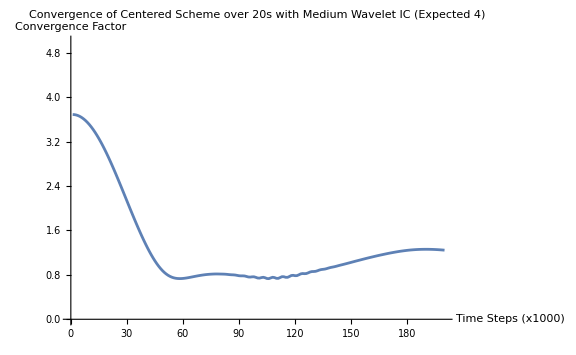

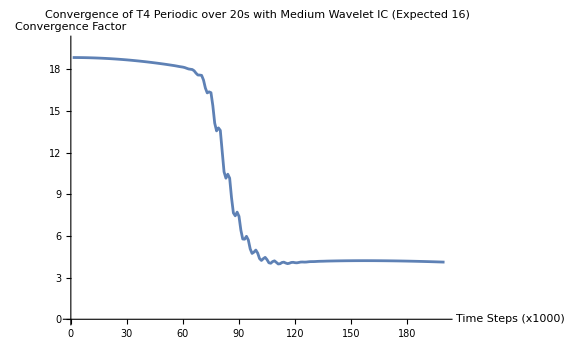

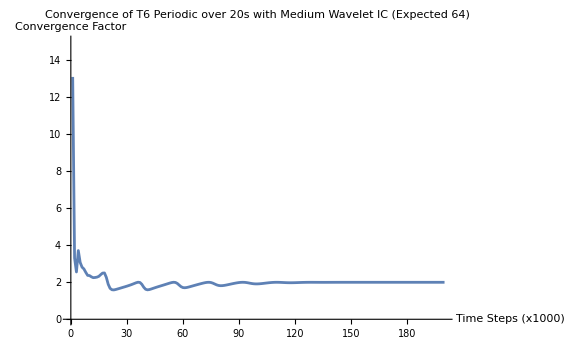

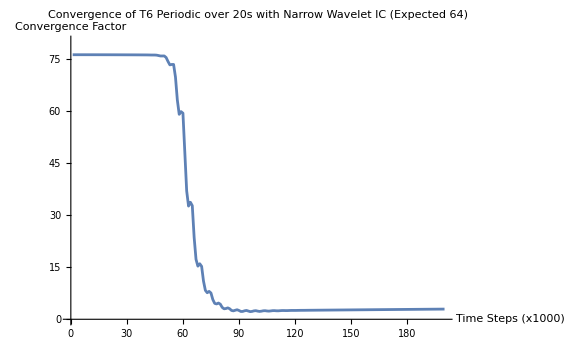

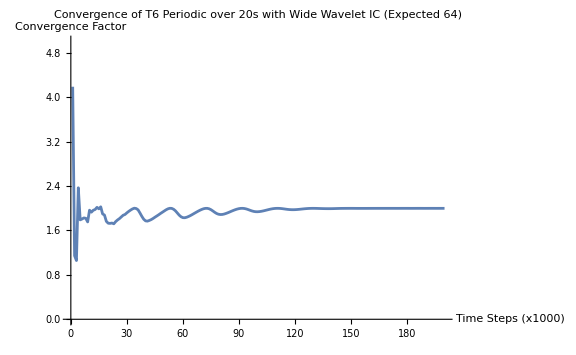

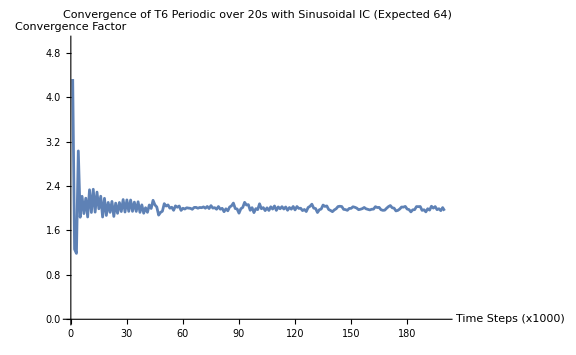

```mathematica
QCenteredScheme={3.6891356178870307,3.6866483211942196,3.6795395779172613,3.6678323675216427,3.65156455006738,3.6307887030919748,3.6055718958072336,3.5759954023430973,3.5421543562502222,3.5041573489380315,3.462125975179933,3.4161943292557737,3.3665084557253566,3.3132257592351895,3.2565143781495367,3.1965525271721864,3.1335278144814835,3.067636539243661,2.9990829756966386,2.928078650309185,2.8548416188222343,2.779595750265916,2.7025700253192606,2.6239978566340225,2.5441164389696693,2.46316613717056,2.381389920128998,2.299032848881185,2.2163416268106544,2.1335642194892146,2.0509495508271667,1.9687472807240392,1.8872076670146158,1.8065815107766718,1.727120178439977,1.649075685864605,1.5727008176911532,1.4982492386460877,1.4259755307999116,1.3561350608140703,1.2889835434058377,1.2247761224688647,1.1637657428419619,1.1062005410839078,1.0523199570736426,1.0023492834227115,0.9564924580618457,0.9149230974946524,0.8777740790628792,0.8451263947167702,0.8169984564979115,0.7933374154328913,0.7740141799614575,0.758823507531469,0.7474897619788284,0.739677921866264,0.7350085994414232,0.7330753894280404,0.7334625960500225,0.7357611116593252,0.7395805328543325,0.7445573508472374,0.7503612783456228,0.7567012192215424,0.7633280096136517,0.7700290548733844,0.7766179807824655,0.7829336565792,0.7888557610305955,0.7943146096929086,0.7992624513330859,0.8036228675568715,0.8072960580351551,0.8102532444791901,0.812601798225919,0.8144637703330109,0.8157541572554405,0.8162065087787088,0.8157748025307477,0.8149128419051347,0.814128676847019,0.8131716339901689,0.811091279564674,0.8075828746376174,0.8039332775332715,0.8016955342221308,0.8002920288594869,0.7970474113247392,0.7907965183951399,0.7844954438354168,0.7820129933319435,0.782490995460347,0.780037013335161,0.7714549745132542,0.762238097608566,0.7601490017428223,0.7645837474206155,0.7652998353886155,0.7554962159694246,0.7434053482556373,0.7416670034103569,0.7508146384844889,0.7566873369532582,0.7477870518581047,0.7339948147027802,0.7324419077451538,0.7453684563720512,0.7568267363598736,0.7512405146588353,0.737945667595417,0.7368207787034733,0.7517256191057949,0.7673398458313923,0.7664771589413499,0.7558963560536921,0.7556709460676552,0.7708582506737867,0.7882616705869571,0.791891089290555,0.7853100355972262,0.7862247845973092,0.800396973987618,0.8173997045666268,0.8241219116753605,0.8216715420905002,0.823696667610891,0.8360071469340146,0.8511815197718026,0.8594556479192887,0.8605999198004657,0.8637811831301001,0.8740255175733148,0.8868371255544649,0.8956961009138757,0.8998753396980672,0.9045788481965351,0.9133174703924195,0.9239978623998254,0.9330268652574855,0.9397302581862552,0.9463686131216497,0.9546706730973421,0.963989359593713,0.9729903345103434,0.9813893000041813,0.9897637845038424,0.998459110625763,1.007306020777519,1.0161694038880573,1.0251530718909527,1.034275879853189,1.0433242541589276,1.052138504192062,1.0608128563078747,1.0695258355628856,1.0783138425334153,1.0870739996033552,1.0956921823779244,1.1040921810687083,1.1122485003744749,1.1202430402095,1.128239166682956,1.136296550063378,1.1442490031054835,1.1518654299716367,1.159133080365828,1.1662860305977165,1.1735140360876488,1.1807230861485911,1.1876490999765852,1.1941641381665946,1.2003901065521543,1.2065087638734655,1.212531739935907,1.2182967257850992,1.2236521020149755,1.2285934705178043,1.233219128743685,1.2375917989259095,1.2416682335814053,1.2453515594831077,1.2485880836060592,1.2514046575861382,1.2538616048881694,1.2559828755418005,1.2577371673833149,1.2590810753550572,1.26000978778243,1.2605605947934546,1.2607725422395328,1.260652317034119,1.2601819358410224,1.2593523963681355,1.2581818490987937,1.256701384409062,1.2549302092351544,1.2528693104398592,1.2505165954874569,1.2478824485904403,1.2449886972444866};
ListPlot[QCenteredScheme,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of Centered Scheme over 20s with Medium Wavelet IC (Expected 4)",PlotRange->{0,5}]


QT4Wavelet={18.862397902077085,18.862124894139704,18.861450603498483,18.86037504722157,18.858898288804436,18.857020437645726,18.854741649042186,18.852062124103245,18.848982109698934,18.845501898439036,18.841621828563106,18.83734228379638,18.8326636933716,18.827586531747105,18.822111318613903,18.81623861866671,18.80996904147373,18.80330324129737,18.7962419169161,18.788785811440007,18.780935712016667,18.77269244979936,18.764056899449415,18.75502997913271,18.745612650261098,18.735805916625754,18.725610825132637,18.715028464577866,18.704059966697184,18.6927065046761,18.680969289308532,18.66884957166438,18.656348648879646,18.643467871507394,18.630208617994324,18.616572243780745,18.60256011136486,18.588173770812634,18.57341503589829,18.558285468076765,18.54278558955441,18.526915626141385,18.510678502154434,18.49408035381292,18.477122066113406,18.45978946699192,18.442067341776095,18.42397845184218,18.405579621886826,18.38685199845077,18.36761016287529,18.34769960954596,18.32739190278776,18.307225100849937,18.28688864484613,18.264642647320958,18.239431876827016,18.213934676429698,18.192201302978802,18.170886566085084,18.137293251170775,18.08664824679029,18.039383243790986,18.01858655829918,17.997897532604735,17.906048529113367,17.734642104356386,17.6013570642417,17.598587995867724,17.575982531591748,17.24252833546232,16.665935618005665,16.31423408459767,16.389567963443373,16.328445228407475,15.391900196958202,14.135394241670486,13.575800434030896,13.791601554096893,13.612448677406185,12.110536580415292,10.626928383925133,10.165521669583152,10.455479410324736,10.169329799570622,8.76126870449608,7.664099176573466,7.456056904133408,7.721744419609171,7.419598915273023,6.423986733389704,5.7829303852448675,5.770613969473116,5.978820537791952,5.710985369114031,5.070949633504911,4.745585187911925,4.8384549946982816,4.987092518431363,4.768392389019898,4.373677741975792,4.238004105958128,4.36676322947874,4.461782860721652,4.297064600376818,4.069148376973621,4.038232205260603,4.15824630924455,4.210607189952284,4.100176452418755,3.9850798517620194,4.003038971712773,4.092100967763937,4.116195717613846,4.0537921423551895,4.008998860867858,4.040275663730188,4.094826113983542,4.104410960920677,4.077124058643775,4.06833625537772,4.094483918666642,4.1226804595444655,4.127041486814571,4.119723324260738,4.123793495719931,4.140002189080828,4.153039841943709,4.156271137780436,4.1571687908851445,4.162954408900778,4.171581872741332,4.17773030830218,4.180716763461467,4.183603800063522,4.18795154900579,4.192504605550622,4.195920303753791,4.198492499932552,4.201124662747672,4.203976385438189,4.206608450170017,4.20880287816846,4.210744771729638,4.212623323899662,4.214407608557381,4.215995226573581,4.2173778792228855,4.218611632681131,4.219721556259375,4.220690135695139,4.221503093229336,4.222167945950797,4.2226961329285775,4.223089208466796,4.2233441090417525,4.2234612112627925,4.223443826031729,4.223294289474465,4.2230133053009675,4.222601621034085,4.222060713147024,4.221392181955812,4.220597320724268,4.219677299175793,4.218633392335474,4.217466946246521,4.216179273149386,4.214771647057907,4.213245347553823,4.211601669380228,4.209841905565536,4.207967340560175,4.205979255750202,4.203878933024381,4.201667652840108,4.199346692315154,4.196917325554585,4.1943808241879195,4.1917384572467835,4.1889914906431,4.186141187080152,4.183188805999357,4.180135603480644,4.176982832094844,4.173731740723999,4.170383574517585,4.166939574712687,4.163400978571934,4.159769019225448,4.156044925592861,4.152229922255492,4.148325229349108,4.144332062491233,4.140251632626867,4.136085145983157,4.131833803931501,4.127498802928203,4.12308133438228,4.118582584603011};
ListPlot[QT4Wavelet,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T4 Periodic over 20s with Medium Wavelet IC (Expected 16)",PlotRange->{0,20}]

QT6WaveletMedium={13.098227360862,3.3072287197420067,2.556974067126167,3.7138210670159344,3.072246536535872,2.8169639072124957,2.7200492632770503,2.534371980488348,2.3721364592055334,2.3611414679657647,2.293259899194157,2.248653269027188,2.2581693833999568,2.2776380529122595,2.3212212752595325,2.414778474616011,2.4962967582854914,2.5035792928257026,2.2644511738211928,1.8927928817904849,1.6724766906357316,1.5957442443511416,1.5864322590699818,1.6082183108131145,1.6375196650177235,1.6670299584644577,1.6978931032909828,1.728358531473781,1.7581493482727282,1.7896691985481799,1.8228240339572748,1.8577157120384333,1.8956592632653544,1.9360258445717267,1.9755152420560707,2.0032617362758196,1.989060195114339,1.8915063444595128,1.734550659476616,1.622623781837023,1.590989464536881,1.605159986311346,1.6356958301824718,1.670177864162459,1.704457313015033,1.7374393550659744,1.7692821125665978,1.8004422537138929,1.8313599883935554,1.862535802964329,1.8942898132135884,1.9264550887123932,1.9579231219333848,1.985330656202689,2.000721860602446,1.9894374517003404,1.935778689006511,1.8462858995827838,1.761024211361038,1.7136226087173976,1.7038583500971316,1.7167165524249948,1.7400972704947333,1.7675388188216616,1.7961554440831968,1.8248049846648848,1.8531081002525283,1.8809701830583863,1.9082914264320727,1.9347551145790558,1.9595574804757667,1.9809886031342487,1.9959195754228236,1.9994745561670382,1.9859936900205484,1.95291385794401,1.9062871290316623,1.8605037359289236,1.828792196391659,1.8154036058488048,1.8172642660548286,1.8291935643391852,1.8468802360198466,1.8674770638006137,1.8892674440913162,1.9112010275918028,1.9325332887699116,1.9525756911020222,1.9705070731447463,1.985236637352843,1.995354864777788,1.9992676279150114,1.995660602933481,1.9843214131968503,1.9669568616339217,1.9472232357978942,1.9295062933484317,1.9171771810159521,1.9116217922743297,1.9124588359492205,1.9183496419396,1.9277164867954828,1.9391220411686265,1.9513779894824705,1.9635211704087847,1.9747533016394598,1.984391341930657,1.9918559030185228,1.9967050590089135,1.9987093676230512,1.9979430164281349,1.9948440389516993,1.9901923046252545,1.984977004183228,1.980185326247257,1.9765959092575474,1.9746530141064709,1.9744508846781963,1.9758048260323096,1.9783563223162133,1.981671042285148,1.9853139333509078,1.9888982751409137,1.99211486873876,1.9947470728300947,1.9966767857047818,1.997881596023141,1.998423403757357,1.9984291909773333,1.9980647615675824,1.9975058731356095,1.996911873996379,1.9964064294316202,1.996067889970481,1.9959283386805438,1.9959807738209978,1.9961906844102868,1.996508383733717,1.9968808307098627,1.9972601669496006,1.9976089671003816,1.9979025647196642,1.9981291165406851,1.9982877243089041,1.9983856246423666,1.9984352318103482,1.9984509539083672,1.9984464402033701,1.998432746526422,1.9984175900897243,1.9984056819361753,1.9983994857351182,1.998399698034162,1.9984056260033396,1.9984155445581768,1.9984273682941285,1.9984394121238165,1.9984507195013557,1.998460844934174,1.9984694905431208,1.9984764615168982,1.9984818477547819,1.9984860429773026,1.9984894907809412,1.998492457848713,1.9984950688012189,1.9984974668077782,1.998499839967098,1.9985023057134932,1.998504845140676,1.9985073690204438,1.9985098147223839,1.9985121808114346,1.998514544261483,1.998517036411631,1.9985197462997748,1.9985226112048153,1.9985254295622557,1.998528006839713,1.998530300046964,1.9985324289589859,1.998534606987452,1.9985370411546912,1.9985398137090313,1.998542772329991,1.9985455878118408,1.9985480012808408,1.9985500793330193,1.998552185431701,1.9985546676167565,1.998557524688985,1.9985604071211056,1.9985629539164562,1.9985651593802143,1.998567359860271,1.9985698693878144,1.9985726391236232,1.9985753478264283,1.9985777799420652,1.9985800650460055};
ListPlot[QT6WaveletMedium,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T6 Periodic over 20s with Medium Wavelet IC (Expected 64)",PlotRange->{0,15}]

QT6WaveletSmall={76.25802589390514,76.25803857592463,76.25797880301371,76.25784657405765,76.25764187425773,76.25736469593504,76.25701502081576,76.25659284479445,76.25609815057139,76.25553093439086,76.25489118302019,76.25417888933569,76.2533940464659,76.252536645442,76.25160668154625,76.25060414800203,76.2495290377536,76.24838135064235,76.24716107635709,76.24586822538069,76.24450276741621,76.24306470725955,76.24155401599216,76.23997078917319,76.23831499706525,76.23658638988113,76.23478441905672,76.23290934406494,76.23096280258879,76.22894477394584,76.22684746904478,76.22465914471188,76.22238831391542,76.22007319544238,76.21770534812708,76.2151128745778,76.21208297151968,76.20884197351083,76.20610489894808,76.2035609055277,76.19815704984804,76.18688947657485,76.17431441021789,76.17103040148822,76.17002506682722,76.12813428057373,76.01360246687788,75.89661282332285,75.89890783611561,75.90880236883685,75.45166631311534,74.32066889124751,73.3334163960454,73.45245190483253,73.45585076528232,69.81802613589021,63.20282983939291,59.07481933275271,59.85351473788227,59.407335420480166,48.15827897479875,36.992710617092435,32.629280671198714,33.73017683971231,32.74872220208348,23.572099773505077,17.27038922692606,15.311957700573773,16.003848038028423,15.253380297947176,11.006256694924515,8.340789072652647,7.642455392774021,8.041482920453905,7.567623907354359,5.678361781456395,4.579047578780125,4.4137377049295985,4.679135615233861,4.3537896662414015,3.4381853670791687,3.017140976258478,3.0929985525253656,3.2911138825924375,3.034923181049333,2.5431789584476063,2.4285195368936807,2.59982482737633,2.744855753329637,2.531695600928939,2.247512013836622,2.262302670498009,2.4469732874054717,2.542492857071202,2.371114292320927,2.205203243987514,2.2659288260739765,2.4244316046867924,2.478181885791391,2.351548243713501,2.2617246383639085,2.3305757019849183,2.447894411586269,2.471758667320972,2.389124517459727,2.3493677287966563,2.4086391278764716,2.483780770127983,2.4907338212932273,2.445708267001542,2.4357050846153405,2.47799499170215,2.5189566000928685,2.5197464118722297,2.5014866541632474,2.505128171520252,2.53041448308755,2.5495793491727685,2.550445851076057,2.547176985449303,2.5541908634172117,2.5674330356838437,2.5762309042366005,2.57898059850906,2.5818566396532083,2.5881673825027995,2.595405246710746,2.600815873992389,2.6049162082394037,2.609458550915839,2.6147493160091373,2.619969598713345,2.624732276162335,2.6293557582306755,2.634132319003089,2.6389929610795244,2.643788150597607,2.6485194236400185,2.653258454033641,2.6580210951924967,2.6627796848569445,2.6675232470432952,2.672262681888878,2.6770045935060494,2.6817449662771744,2.68648009469981,2.6912111119966493,2.695939747629177,2.7006656368233517,2.7053878024170976,2.7101061098600256,2.7148208743727023,2.719532155357638,2.724239781815179,2.728943646596895,2.733643755319829,2.738340119618113,2.74303271369661,2.747721502829501,2.7524064648260658,2.7570875847269716,2.761764845875139,2.766438229271249,2.7711077160729998,2.775773288464462,2.780434929057741,2.7850926203808464,2.7897463449587856,2.7943960854248795,2.7990418245728046,2.8036835453206885,2.8083212306398595,2.812954863637939,2.817584427483599,2.8222099054767043,2.8268312809977014,2.8314485375254184,2.8360616586443097,2.8406706280212473,2.8452754294331664,2.8498760467426534,2.854472463908484,2.8590646649955302,2.863652634138384,2.868236355599832,2.8728158137007505,2.877390992882118,2.881961877667028,2.886528452664263,2.8910907025943575,2.895648612245496,2.900202166518756,2.904751350390792,2.9092961489392026,2.9138365473252374,2.918372530803519,2.9229040847210457,2.9274311945023337,2.9319538456822505,2.9364720238583297};
ListPlot[QT6WaveletSmall,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T6 Periodic over 20s with Narrow Wavelet IC (Expected 64)",PlotRange->{0,80}]

QT6WaveletLarge={4.189365747393949,1.1447854398103074,1.0580289346293925,2.3690672388858403,1.7908783176626282,1.8065567978174906,1.826271664073239,1.8188522533549767,1.7542585144425882,1.9654336923127191,1.929087823395203,1.9637879993760339,1.977817864293931,2.016937993318649,1.9894098680641368,2.0260735468699167,1.8981336628757264,1.8777975863983067,1.76461477077015,1.7303549820499493,1.7275912919014436,1.7338510012554376,1.7198625381878392,1.7598975809936883,1.7893605447764798,1.8132827636197744,1.8438765908459738,1.874056341040827,1.8881239587055543,1.9177886359524832,1.9442977945973237,1.9676161008136488,1.9883234280660622,2.001358099465302,1.9949591119248005,1.9710348069283816,1.9150359154640748,1.8544298506159334,1.8025808268273769,1.772657925856487,1.7682626626924733,1.7804104824517921,1.7955382387399361,1.8156376398704592,1.838682194373486,1.86035201699656,1.8825390156215158,1.9064133710294136,1.9284623687133722,1.9508430471655636,1.972955416942486,1.9902506594596956,1.999615087564269,1.9977105507075021,1.982019032820127,1.953411664193311,1.9145823716644366,1.875628055510407,1.8461532777832166,1.8306905669367122,1.8293199047352022,1.8380672061703305,1.8518476266340553,1.868246693369786,1.886935865744834,1.9067462448022048,1.9261469194016967,1.9450735470427805,1.9626597634958691,1.9781659777522034,1.9908307992257763,1.998187736863449,1.9985506516560039,1.9907484322336646,1.974411233200706,1.9516257052616415,1.9270533808370398,1.906096522552742,1.8926752560717184,1.8869943903704256,1.8882525834198856,1.8952267327115893,1.906070994239619,1.9188449069862585,1.932839187206723,1.9474011984522446,1.9614018409936347,1.9741503025138043,1.9850779002744035,1.9933162738516947,1.998105754484425,1.998674054850977,1.9947983210343787,1.9867210215107876,1.9753177050527075,1.9626544102481196,1.9511372485190839,1.9424230418868675,1.9377409324857031,1.9372778545986413,1.9401963388383263,1.9454914937658643,1.9525239366404363,1.960655928751157,1.9691934535846203,1.977613639606413,1.985268701457518,1.99152763347337,1.995930258434013,1.9982520496525027,1.998553901127051,1.9968724889415377,1.9934918389764886,1.9890224072670528,1.9841454271072174,1.9796849853430047,1.9764159555957836,1.9745241772324285,1.9740155515462032,1.974920691444947,1.9770440812233572,1.9800415235711635,1.983523226122899,1.9871458704175253,1.9905581617804808,1.9935289302763881,1.9959409031197515,1.9976023314569977,1.9984572462404127,1.9985472138870386,1.998025253779621,1.9970678906508332,1.995881175983869,1.9947503615832949,1.993839284535177,1.9931750885995452,1.9928176546300937,1.9926872515027731,1.99283243149922,1.9933300440562243,1.9941765202595179,1.9951911477358242,1.996203073657569,1.9970623778171703,1.9976305658307068,1.9979458741515779,1.998156548526134,1.9983449262718924,1.9985035713096657,1.9985478083891064,1.9984218922905592,1.9981954142110594,1.99797101825434,1.997837820686227,1.9978159197596963,1.9978525868732713,1.9978859844368924,1.9979050370940346,1.9979529458288925,1.998055682857502,1.9981838680971769,1.9982979487826995,1.9983789712035338,1.9984356407531936,1.9984708360481762,1.9984931177775758,1.998503294799551,1.9985180914861418,1.9985412544314507,1.998575972976566,1.9985866369834417,1.9985599451833216,1.9984801531241336,1.9983964009463135,1.998367643537835,1.9984347917613299,1.9985591322876874,1.9986829621390014,1.9987123413801628,1.9986294938051967,1.998473302358293,1.9983596835860142,1.9983596406911595,1.9984924874779624,1.9986590911711677,1.9987531259760178,1.9986973309304172,1.9985525804404085,1.9984260890997028,1.9984270534238338,1.9985309556738269,1.9986498546468385,1.998675744931415,1.998612904612321,1.9985254167766844,1.9985060035107622,1.9985495379606415,1.9986105228119888,1.9986216319905237,1.9985928176601748};
ListPlot[QT6WaveletLarge,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T6 Periodic over 20s with Wide Wavelet IC (Expected 64)",PlotRange->{0,5}]

QT6Sinusoid={4.327981856710551,1.2612755978396892,1.1870814350724932,3.0327807639797872,1.8383042962656546,2.2157312277013044,1.9041819811660883,2.181727013879161,1.8430523512495742,2.3330218714809665,1.9238544828160307,2.342414003634488,1.930185922790983,2.2912958746504923,1.9906507833890648,2.2171424049887065,1.842536661115082,2.1794926099332255,1.8701545709883414,2.105349939305793,1.926737072345224,2.1232543137064535,1.8526791526698956,2.0926131809684936,1.9086884292733326,2.1040279053511206,1.941050997429559,2.156947727591065,1.9319160334104544,2.1507044739120316,1.9441207994046217,2.1485519611274633,1.9444377737129834,2.1104459351238316,1.9435858980208651,2.117126839980518,1.92618335852355,2.0608948575150756,1.9106877578205208,2.0099184106896715,1.9268965078060256,2.059116648540048,1.9960871495428254,2.1428472822284914,2.060828556763626,2.0227845908511557,1.8765321174514606,1.9256796541936947,1.9463695271140924,2.0832060080211017,2.039389716963826,2.0604993271905823,2.0013289360646787,2.018918229158511,1.9632561038629932,2.043036779683634,2.0186291210751137,2.0404317519210773,1.9615411601273463,2.000396740910813,1.9861974709018106,2.0086833150944834,2.002878800955546,1.9988165104917208,1.981314079277755,2.0151062239085293,2.0161398458680018,2.000719889568239,2.014181320671992,2.0102074475047393,2.0244664796568643,2.0006254177809937,2.032839514362313,1.9954419899833853,2.0473672270601435,2.003385157531708,2.010339648890689,1.982650968642971,2.0311720928879358,1.9830539743077853,1.9991286899331684,1.9381954114890747,1.9902409843964821,1.9542337344151932,2.0225741710730194,2.0438520116806598,2.0932940388157273,1.99518190642192,1.9867523367722129,1.9114505099375159,1.9916327680028534,2.0143319432945908,2.1066028185156367,2.0580125483046516,2.0658137066515847,1.9635124742244003,2.010939740645603,1.9212940514070211,1.9933940738162839,1.975722617905609,2.0801412284077854,1.991990353672738,2.0118902721153207,1.9578726346843427,2.0075424001819115,1.9606874711952558,2.026589003933366,1.9859691674088287,2.0413215687203223,1.9618927969230167,2.0232658521654945,1.9903684171932976,2.028500231659636,1.9866623988916294,2.0230709205099933,1.9641411518821863,2.0129278800403334,1.9838908672241211,2.0317183707418476,1.970732201603625,2.0313588373123266,1.9976522566154484,2.000484548886667,1.9578539470650478,1.978129757581164,1.941120382551894,2.013820469570921,2.0351495975139096,2.073443058729963,2.0025902541606415,1.9944263754663218,1.9234788635633067,1.9729209386501527,1.9868529753588482,2.057290643117106,2.033369274047521,2.0416844746100153,1.9775169325012187,1.9599315016186716,1.9386784141898001,1.9701283853936988,1.9911082436038374,2.0308319427635246,2.0364798507243647,2.0310877394186724,1.9805623417620055,1.975739526308463,1.9629330105019789,1.9973328390490368,1.9982551701929068,2.0265054642991327,2.0174925908712282,2.002693732616906,1.9745527087294643,1.9821112288566929,1.9931342451559677,2.0141507564817718,1.9902097112954553,1.9800128135878114,1.9701765635218107,1.9820895444848161,1.9850272145371592,2.028334216778458,2.0129315684720073,2.0158303311617254,1.9736410563796722,1.9625412717258723,1.9655732909084687,2.000029542313284,2.0298392637829843,2.048671271925481,2.0085368671771286,2.002310596699936,1.9523808237379372,1.9616342833151137,1.9856908536953735,2.0217665909298774,2.020805990104121,2.033097439128329,1.9858180873905953,1.976154610957494,1.9350179731767982,1.972645995514545,1.97501098204266,2.03022565202918,2.029274433788092,2.031084747827699,1.9618521078369542,1.9732713795577097,1.9352753037756765,1.9912393739025875,1.9669808148948258,2.036416285565352,2.0027270013445073,2.0299958426277773,1.974570987590328,1.991645554069567,1.9576569733627174,2.0121314026208807,1.955601660821101};
ListPlot[QT6Sinusoid,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence of T6 Periodic over 20s with Sinusoidal IC (Expected 64)",PlotRange->{0,5}]
```

## Convergence Testing (Diffusion)

### Diffusion Equation Setup

```mathematica
Clear[Δt,diffusion];

(*Initialize Parameters*)
Δt=0.001;
(*waveSpeed=0.05;*)
diffusion=0.1;
```

### Setting Up The Operators

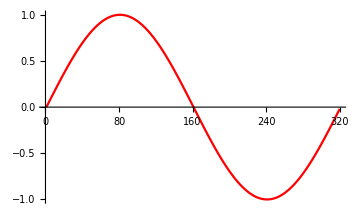

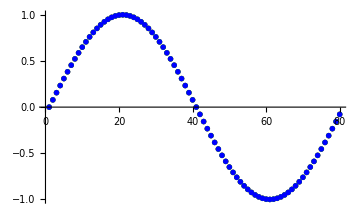

```mathematica
Clear[ϕ1,ϕ2,ϕ3,coeffToUse];

(* Coefficients *)
coeffToUse=coeffNJP62D;
boundaries=0;
(* Initial Condition *)
(*f[x_]:=Exp[-(5x-5/2)^2]Sin[20π x];*)
f[x_]:=Sin[2π x];

(**************************************************************************************)

(* Define the Initial Conditions with n=400,200,100 for each function *)
(* h: n=400 *)
n1=320;

(* 2h: n=200 *)
n2=160;

(* 4h: n=100 *)
n3=80;

(* This will reset the initial conditions *)
Reset[]:=Module[{},
ϕ1=Array[f[#]&,n1,{0,1-1/n1}];
ϕ2=Array[f[#]&,n2,{0,1-1/n2}];
ϕ3=Array[f[#]&,n3,{0,1-1/n3}];
];
Reset[];

(* Setting up the Derivative Operators based on the LHS and RHS matrices and the precalculated Inverses *)
(* Set up Derivative Operator Q1 *)
LHS1=PeriodicLHS[n1,coeffToUse];
RHS1=PeriodicRHS2D[n1,coeffToUse];

RHS1=(n1)RHS1;
Q1=Inverse[LHS1].RHS1;
ctQ1=diffusion Δt Q1;

(* Set up Derivative Operator Q2 *)
LHS2=PeriodicLHS[n2,coeffToUse];
RHS2=PeriodicRHS2D[n2,coeffToUse];

RHS2=(n2)RHS2;
Q2=Inverse[LHS2].RHS2;
ctQ2=diffusion Δt Q2;

(* Set up Derivative Operator Q3 *)
LHS3=PeriodicLHS[n3,coeffToUse];
RHS3=PeriodicRHS2D[n3,coeffToUse];

RHS3=(n3)RHS3;
Q3=Inverse[LHS3].RHS3;
ctQ3=diffusion Δt Q3;


(* This module calculates the convergence factor between the functions at points that are common to all of them. The lasts points are excluded as they are repeats of the first *)
GetQ[]:=Module[{ϕ1a,ϕ2a,ϕ3a},
ϕ1a=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a=Table[ϕ3[[i]],{i,1,n3}];
If[Norm[ϕ2a-ϕ1a]!=0,Norm[ϕ3a-ϕ2a]/Norm[ϕ2a-ϕ1a],0]//N
];

ListPlot[ϕ1,Joined->True,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red]

(*GetQ[]*)

ϕ1a2=Table[ϕ1[[4i-3]],{i,1,n3}];
ϕ2a2=Table[ϕ2[[2i-1]],{i,1,n3}];
ϕ3a2=Table[ϕ3[[i]],{i,1,n3}];
Show[ListPlot[ϕ1a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Red],
ListPlot[ϕ2a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Green],
ListPlot[ϕ3a2,Joined->False,ImageSize->Medium,PlotRange->{-1,1},PlotStyle->Blue]
]
```

### Running the Operators

```mathematica
Clear[Q,Q2,Q3,ϕ1graph,ϕ2graph,ϕ3graph,ϕ4graph,ϕ5graph];

(* Reset to initial conditions *)
Reset[];

(* Initialize the data collection for plotting *)
Q={};
Q2={};
Q3={};
ϕ1graph={};
ϕ2graph={};
ϕ3graph={};
ϕ4graph={};
ϕ5graph={};

(* This loop runs for every step and will update the functions based on the derivative operators *)
For[i=0,i<10000,i++,
(* Update the functions *)
ϕ1=ϕ1+ctQ1.ϕ1;
ϕ2=ϕ2+ctQ2.ϕ2;
ϕ3=ϕ3+ctQ3.ϕ3;

(* Collect data points every 1000 steps *)
If[Mod[i,1000]==0,
AppendTo[Q,GetQ[]];
AppendTo[ϕ1graph,ListPlot[ϕ1,Joined->True,PlotRange->{-1,1}]];AppendTo[ϕ2graph,ListPlot[ϕ2,Joined->True,PlotRange->{-1,1}]];
AppendTo[ϕ3graph,ListPlot[ϕ3,Joined->True,PlotRange->{-1,1}]];
];
];
```

### Plotting Results

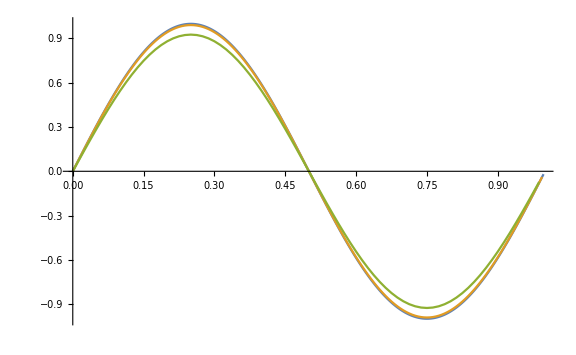

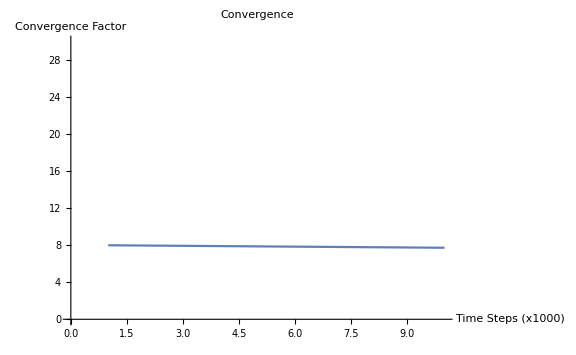

```mathematica
(*ListAnimate[ϕ1graph,ImageSize->Medium]
ListAnimate[ϕ2graph,ImageSize->Medium]
ListAnimate[ϕ3graph,ImageSize->Medium]
ListAnimate[ϕ4graph,ImageSize->Medium]
ListAnimate[ϕ5graph,ImageSize->Medium]*)

p1=Transpose[{Table[i/Length[ϕ1],{i,0,Length[ϕ1]-1}],ϕ1}];
p2=Transpose[{Table[i/Length[ϕ2],{i,0,Length[ϕ2]-1}],ϕ2}];
p3=Transpose[{Table[i/Length[ϕ3],{i,0,Length[ϕ3]-1}],ϕ3}];

ListPlot[{p1,p2,p3},Joined->True,ImageSize->Large, PlotRange->{-1,1}]


(*ϕ1graph[[50]]
ϕ2graph[[50]]
ϕ3graph[[50]]*)

(* Plot the convergence Factor *)
ListPlot[Q,Joined->True,AxesLabel->{"Time Steps (x1000)","Convergence Factor"},ImageSize->Large,PlotLabel->"Convergence",PlotRange->{0,30}]
```

```mathematica
Q
```

{2.,1.9963,1.99261,1.98893,1.98526,1.98159,1.97793,1.97428,1.97063,1.967,1.96337,1.95974,1.95613,1.95252,1.94892,1.94533,1.94174,1.93817,1.9346,1.93103,1.92748,1.92393,1.92039,1.91685,1.91333,1.90981,1.90629,1.90279,1.89929,1.8958,1.89232,1.88884,1.88537,1.88191,1.87845,1.875,1.87156,1.86813,1.8647,1.86128,1.85787,1.85446,1.85106,1.84767,1.84428,1.84091,1.83753,1.83417,1.83081,1.82746,1.82411,1.82078,1.81745,1.81412,1.81081,1.8075,1.80419,1.80089,1.7976,1.79432,1.79104,1.78777,1.78451,1.78125,1.778,1.77476,1.77152,1.76829,1.76507,1.76185,1.75864,1.75543,1.75224,1.74905,1.74586,1.74268,1.73951,1.73634,1.73319,1.73003,1.72689,1.72375,1.72061,1.71749,1.71436,1.71125,1.70814,1.70504,1.70194,1.69885,1.69577,1.69269,1.68962,1.68656,1.6835,1.68045,1.6774,1.67436,1.67133,1.6683,1.66528,1.66226,1.65925,1.65625,1.65325,1.65026,1.64728,1.6443,1.64133,1.63836,1.6354,1.63244,1.62949,1.62655,1.62361,1.62068,1.61776,1.61484,1.61192,1.60902,1.60611,1.60322,1.60033,1.59744,1.59456,1.59169,1.58882,1.58596,1.58311,1.58026,1.57741,1.57458,1.57174,1.56892,1.56609,1.56328,1.56047,1.55766,1.55487,1.55207,1.54929,1.5465,1.54373,1.54096,1.53819,1.53543,1.53268,1.52993,1.52719,1.52445,1.52172,1.51899,1.51627,1.51355,1.51084,1.50814,1.50544,1.50274,1.50005,1.49737,1.49469,1.49202,1.48935,1.48669,1.48403,1.48138,1.47874,1.4761,1.47346,1.47083,1.46821,1.46559,1.46297,1.46036,1.45776,1.45516,1.45257,1.44998,1.44739,1.44481,1.44224,1.43967,1.43711,1.43455,1.432,1.42945,1.42691,1.42437,1.42184,1.41931,1.41679,1.41427,1.41176,1.40925,1.40675,1.40425,1.40176,1.39927,1.39679,1.39431,1.39184,1.38937,1.38691,1.38445,1.382,1.37955,1.37711,1.37467,1.37223,1.36981,1.36738,1.36496,1.36255,1.36014,1.35773,1.35533,1.35294,1.35055,1.34816,1.34578,1.3434,1.34103,1.33866,1.3363,1.33394,1.33159,1.32924,1.3269,1.32456,1.32222,1.31989,1.31757,1.31525,1.31293,1.31062,1.30831,1.30601,1.30371,1.30142,1.29913,1.29684,1.29456,1.29229,1.29002,1.28775,1.28549,1.28323,1.28098,1.27873,1.27648,1.27424,1.27201,1.26978,1.26755,1.26533,1.26311,1.2609,1.25869,1.25648,1.25428,1.25208,1.24989,1.2477,1.24552,1.24334,1.24117,1.239,1.23683,1.23467,1.23251,1.23036,1.22821,1.22606,1.22392,1.22178,1.21965,1.21752,1.2154,1.21328,1.21116,1.20905,1.20694,1.20484,1.20274,1.20064,1.19855,1.19646,1.19438,1.1923,1.19023,1.18815,1.18609,1.18402,1.18197,1.17991,1.17786,1.17581,1.17377,1.17173,1.1697,1.16767,1.16564,1.16362,1.1616,1.15958,1.15757,1.15556,1.15356,1.15156,1.14956,1.14757,1.14558,1.1436,1.14162,1.13964,1.13767,1.1357,1.13374,1.13178,1.12982,1.12786,1.12591,1.12397,1.12203,1.12009,1.11815,1.11622,1.1143,1.11237,1.11045,1.10854,1.10662,1.10472,1.10281,1.10091,1.09901,1.09712,1.09523,1.09334,1.09146,1.08958,1.0877,1.08583,1.08396,1.0821,1.08024,1.07838,1.07653,1.07468,1.07283,1.07099,1.06915,1.06731,1.06548,1.06365,1.06182,1.06,1.05818,1.05637,1.05456,1.05275,1.05094,1.04914,1.04734,1.04555,1.04376,1.04197,1.04019,1.03841,1.03663,1.03486,1.03309,1.03132,1.02956,1.0278,1.02604,1.02429,1.02254,1.02079,1.01905,1.01731,1.01557,1.01384,1.01211,1.01038,1.00866,1.00694,1.00522,1.00351,1.0018,1.00009,0.998389,0.996689,0.994992,0.993299,0.991608,0.989921,0.988237,0.986556,0.984878,0.983204,0.981533,0.979865,0.9782,0.976538,0.97488,0.973225,0.971572,0.969923,0.968278,0.966635,0.964995,0.963359,0.961726,0.960095,0.958468,0.956844,0.955223,0.953605,0.951991,0.950379,0.94877,0.947165,0.945562,0.943963,0.942366,0.940773,0.939183,0.937595,0.936011,0.93443,0.932851,0.931276,0.929704,0.928134,0.926568,0.925005,0.923444,0.921887,0.920332,0.918781,0.917232,0.915686,0.914143,0.912604,0.911067,0.909533,0.908002,0.906473,0.904948,0.903426,0.901906,0.900389,0.898876,0.897365,0.895856,0.894351,0.892849,0.891349,0.889852,0.888359,0.886867,0.885379,0.883894,0.882411,0.880931,0.879454,0.87798,0.876508,0.875039,0.873573,0.87211,0.87065,0.869192,0.867737,0.866285,0.864835,0.863389,0.861945,0.860503,0.859065,0.857629,0.856195,0.854765,0.853337,0.851912,0.850489,0.84907,0.847652,0.846238,0.844826,0.843417,0.84201,0.840606,0.839205,0.837807,0.836411,0.835017,0.833626,0.832238}